# MGDrivE: Aggregate Landscape Analysis

```mathematica
(*Set the path for the experiments*)
USER=3;
return=If[USER==1,SetDirectory["/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR"],1];
return=If[USER==2,SetDirectory["/Volumes/Pusheen/xjego-khuq3/MCR"],1];
return=If[USER==3,SetDirectory["/Users/sanchez.hmsc/Desktop/MCR"],1];
If[return==1,Print["PATH ERROR"],Print["Path setup correctly"]];
(*Set a name for the outputs and define experiment's ranges*)
experimentName="MCR_AL_";
{releasesStart,releasesInterval,timeRange}={25,7,{1,365*3-1}};
(*Select the aggregation indices for genotypes*)
genotypesGroups={
{{2,5,5,6,7},"H"},
{{1,1,2,3,4},"W"},
{{3,6,8,8,9},"R"},
{{4,7,9,10,10},"B"}
};
(*Define genotypes colors*)
originalColorsValues={
{0,100,70,0},
{70,50,0,0},
{50,100,0,0},
{0,100,0,0}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors;
Transpose[{rgbColors,genotypesGroups[[All,2]]}]//Grid
```

Path setup correctly

RGBColor[1., 0., 0.30000000000000004] | H
RGBColor[0.30000000000000004, 0.5, 1.] | W
RGBColor[0.5, 0., 1.] | R
RGBColor[1., 0., 1.] | B

## 0) Functions

```mathematica
AggregateByGenotype[rawDataTotal_,genotypesGroups_]:=Module[{aggregatedData,outputTotals,totals,transposedTotals},
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
transposedTotals
]
GenerateMatrixPlotsNonNormalized[aggregatedGroupData_,timeRange_,maxesMax_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1/maxPopSize]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
GenerateStreamChart[counts_]:=BarChart[counts//Transpose
,PerformanceGoal->"Speed"
,AspectRatio->1/4
,Axes->False
,FrameLabel->(Style[#,50]&/@{"Time","Genotype Breakdown"})
,BarSpacing->{0,0}
,ChartLayout->"Stacked"
,ChartStyle->(Directive[Opacity[.6],Lighter[#,0],EdgeForm[None]]&/@rgbColors)
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameTicks->{{None,Range[0,10000,100]},{Range[0,1.5*counts//Flatten//Max,250],None}}
,FrameTicksStyle->{
{Directive[Black,25],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,25]}
}
(*,GridLines->{Range[0,50000,100],Range[0,1.5*counts//Flatten//Max,100]}*)
,GridLinesStyle->Directive[Gray,Dashed]
,ImagePadding->Automatic
,ImageSize->2000
,PlotRangePadding->{0,0}
,PlotRange->{{timeRange[[1]],All},{0,1.1*Max[Total/@Transpose[counts]]}}
,Epilog->Flatten[{Thickness[.001],Dashed,(Line[{{#,0},{#,1.1*Max[Total/@Transpose[counts]]}}]&/@{releaseTimes[[1]]})}]
]
GetMaxPopulation[aggregatedGroupData_,genotypesGroups_,timeRange_]:=Module[{i,maxes,genotypeA,genotypeAtemp,maxesMax},
i=1;
maxes=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeAtemp=Max[#]&/@genotypeA
,{i,1,genotypesGroups//Length}];
maxesMax=Max/@Transpose[maxes];
maxesMax
]
GenerateMatrixPlotsSplits[matrixPlots_]:=GraphicsGrid[Prepend[
Transpose[{Show[#,FrameTicks->None]&/@matrixPlots}],
{Show[matrixPlots,FrameTicks->None]}
]]
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateMatrixPlots[aggregatedGroupData_,timeRange_,maxesMax_,rgbaColors_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeA=genotypeA/maxesMax;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
CalculateCounts[aggregatedGroupData_,genotypesGroups_]:=Module[{genotypeTemp,genotypeTotal},
Table[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}]
]
```

## 1) Single Experiment Dynamics

```mathematica
(*Homing rate, Female deposition amount, H-allele fitness, B-allele fitness*)
experimentString="E_090_075_002_010";
```

Load Data

```mathematica
experimentFolders=FileNames[experimentString,Directory[]]
cellFolder=experimentFolders[[1]];
sweepID={null,homing,femaleDeposition,hCost,bCost}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last)
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean*","AF1_Mean*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&
```

{/Users/sanchez.hmsc/Desktop/MCR/E_090_075_002_010}

{ⅇ,90,75,2,10}

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
WW | WH | WR | WB | HH | HR | HB | RR | RB | BB

Aggregate Data By Genotype

```mathematica
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups];
maxPopSize=aggregatedGroupData//Flatten//Max;
```

Export Color Palette

```mathematica
SwatchLegend[rgbColors,genotypesGroups[[All,2]]
,LabelStyle->30
,LegendMarkerSize->25
]
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
Export["./images/"<>"00_ColorSwatch.png",%%,ImageResolution->500];
```

Plot

### Normalized

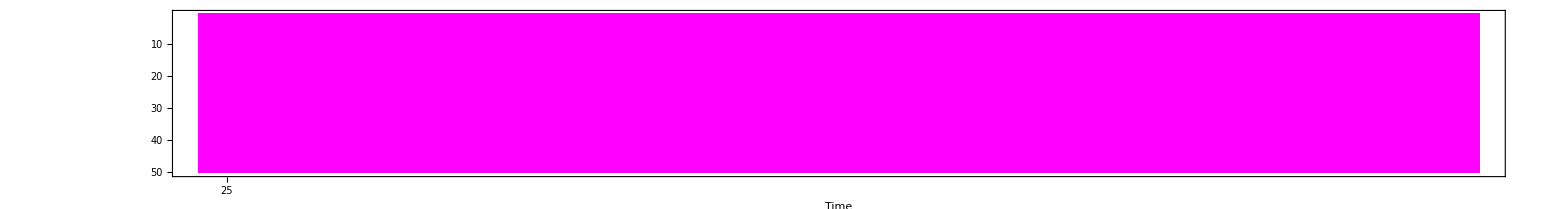

./images/E_090_075_002_010-02.png

```mathematica
maxesMax=GetMaxPopulation[aggregatedGroupData,genotypesGroups,timeRange];
(*matrixPlotsNM=GenerateMatrixPlots[aggregatedGroupData,timeRange,maxesMax];*)
matrixPlotsNN=GenerateMatrixPlotsNonNormalized[aggregatedGroupData,timeRange,maxesMax];
(*matrixPlotsCombinedNM=Show[matrixPlotsNM]*)
matrixPlotsCombinedNN=Show[matrixPlotsNN]
(*Export["./images/"<>experimentString<>"-01.png",matrixPlotsCombinedNM,ImageSize->5000]*)
Export["./images/"<>experimentString<>"-02.png",matrixPlotsCombinedNN,ImageSize->5000]
```

### Normalized Split

```mathematica
matrixPlotsSplit=GenerateMatrixPlotsSplits[matrixPlotsNN];
Export["./images/"<>experimentString<>"-03.png",matrixPlotsSplit,ImageSize->5000]
```

./images/E_090_075_002_010-03.png

### BarChart

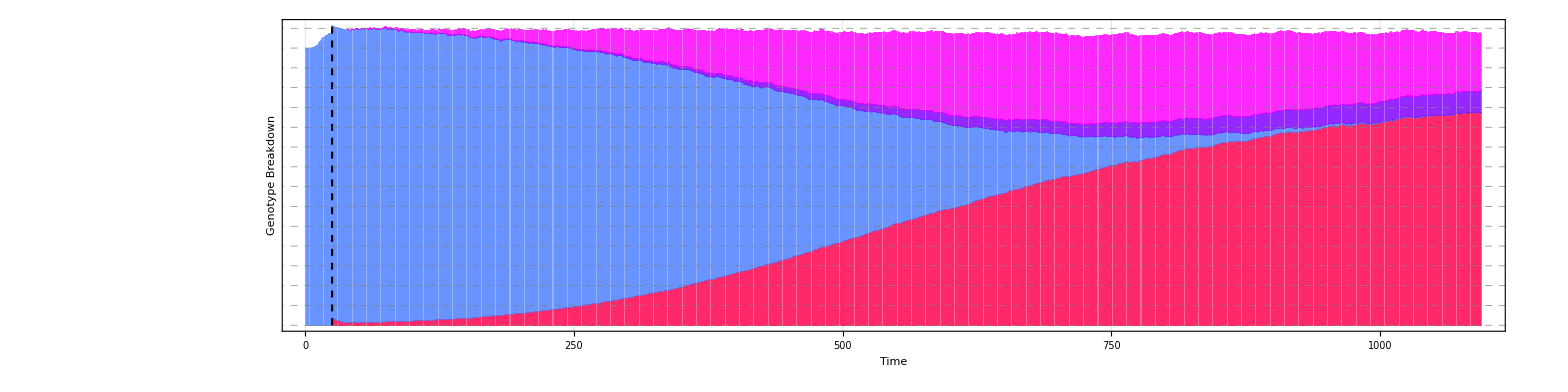

./images/E_090_075_002_010-04.png

```mathematica
counts=CalculateCounts[aggregatedGroupData,genotypesGroups];
streamChart=GenerateStreamChart[counts]
Export["./images/"<>experimentString<>"-04.png",streamChart,ImageSize->2500]
```

## 2) Single Experiment Batch

```mathematica
folderNames=Last/@(StringSplit[#,"/"]&/@FileNames["E_*",Directory[]]);
Print[ToString[Length[folderNames]]<>" folders loaded"];
```

2833 folders loaded

```mathematica
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
(*Export plots loop*)
Table[
(*Process folders for analysis*)
experimentFolders=FileNames[folderNames[[i]],Directory[]];
cellFolder=experimentFolders[[1]];
sweepID={null,homing,femaleDeposition,hCost,bCost}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean*","AF1_Mean*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
(*Aggregate by genotype*)
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups];
(*Plot 1*)
maxPopSize=aggregatedGroupData//Flatten//Max;
maxesMax=GetMaxPopulation[aggregatedGroupData,genotypesGroups,timeRange];
(*matrixPlotsNM=GenerateMatrixPlots[aggregatedGroupData,timeRange,maxesMax];*)
matrixPlotsNN=GenerateMatrixPlotsNonNormalized[aggregatedGroupData,timeRange,maxesMax];
(*Plot 2*)
matrixPlotsSplit=GenerateMatrixPlotsSplits[matrixPlotsNN];
(*Plot 3*)
counts=CalculateCounts[aggregatedGroupData,genotypesGroups];
streamChart=GenerateStreamChart[counts];
(*Export plots*)
fileName=StringSplit[cellFolder,"/"]//Last;
(*Export["./images/"<>fileName<>"-01.png",matrixPlotsCombinedNM,ImageSize->2500];*)
Export["./images/"<>fileName<>"-02.png",matrixPlotsCombinedNN,ImageSize->2500];
Export["./images/"<>fileName<>"-03.png",matrixPlotsSplit,ImageSize->2500];
Export["./images/"<>fileName<>"-04.png",streamChart,ImageSize->2000];
,{i,1,folderNames//Length}]
```

$Aborted

## 3) Factorial Grid

Load Data

```mathematica
(*:--------: User Input    :--------:*)
{experimentName,experimentFilter}={"MCR/2018_08_24_ANALYZED","E*"};
timeRange={1,365*10-1};
releasesStart=20;
genotypesGroups={
{{2,6,6,7,8,9},"H"},
{{1,1,2,3,4,5},"W"},
{{3,10,10,11,12},"R"},
{{4,8,11,13,13},"B"}
};
(*:--------: Get Folders   :--------:*)
directoryData=Directory[]<>"/"<>experimentName<>"/";
experimentFolders=FileNames[experimentFilter,directoryData];
Length[experimentFolders]
```

```mathematica
factorialData=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,geography,driveSystem,homing,resistant,broken}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM*","AF1*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
(*Aggregate by group*)
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
aggregatedGroupData=transposedTotals;
(*Mosquito counts*)
counts=ParallelTable[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}];
(*Mosquito Ratios*)
ratio=(#[[2]]/(#[[1]]+#[[2]])&/@{counts})[[1]];
ratioTime=Transpose[{Range[ratio//Length],counts[[1]],counts[[2]],counts[[3]],counts[[4]]}];
Flatten/@({ConstantArray[{homing,resistant,broken},ratio//Length],ratioTime}//Transpose)
,{i,1,experimentFolders//Length}];
flattenedData=Flatten[factorialData,1];
```

Plot Data

```mathematica
{day,{min,max}}={75,{.3,1}};
selectedDataSliceA=Cases[flattenedData,{hIn_,rIn_,bIn_,Round[day],hOut_,wOut_,rOut_,bOut_}->{hIn/100,rIn/100,bIn/100,(wOut+rOut+bOut)/(hOut+wOut+rOut+bOut)}];
selectedDataSliceB=Cases[flattenedData,{hIn_,rIn_,bIn_,Round[day],hOut_,wOut_,rOut_,bOut_}->{hIn/100,rIn/100,bIn/100,hOut/(hOut+wOut+rOut+bOut)}];
neutralPlot=ListDensityPlot3D[
selectedDataSliceA
,AxesLabel->(Style[#,30]&/@{"H","R","B"})
,AxesStyle->Directive[25]
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"DeepSeaColors",{max,min}}]
,ImageSize->750
,OpacityFunction->Interval[{min,max}]
,PlotLabel->Style["Wild and Neutral Fraction\n",40]
,PlotRange->{{0,All},{0,All},{0,All}}
,ViewPoint->{-3,3,3}
];
homingPlot=ListDensityPlot3D[
selectedDataSliceB
,AxesLabel->(Style[#,30]&/@{"H","R","B"})
,AxesStyle->Directive[25]
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"ValentineTones",{max,min}}]
,ImageSize->750
,OpacityFunction->Interval[{min,max}]
,PlotLabel->Style["Homing Fraction\n",40]
,PlotRange->{{0,All},{0,All},{0,All}}
,ViewPoint->{-3,3,3}
];
GraphicsGrid[{
{neutralPlot,homingPlot}
}
,ImageSize->2000
]
```

Animated Data

```mathematica
Table[
{min,max}={.3,1};
selectedDataSliceA=Cases[flattenedData,{hIn_,rIn_,bIn_,Round[day],hOut_,wOut_,rOut_,bOut_}->{hIn/100,rIn/100,bIn/100,(wOut+rOut+bOut)/(hOut+wOut+rOut+bOut)}];
selectedDataSliceB=Cases[flattenedData,{hIn_,rIn_,bIn_,Round[day],hOut_,wOut_,rOut_,bOut_}->{hIn/100,rIn/100,bIn/100,hOut/(hOut+wOut+rOut+bOut)}];
neutralPlot=ListDensityPlot3D[
selectedDataSliceA
,AxesLabel->(Style[#,30]&/@{"H","R","B"})
,AxesStyle->Directive[25]
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"DeepSeaColors",{max,min}}]
,ImageSize->750
,OpacityFunction->Interval[{min,max}]
(*,PerformanceGoal->"Speed"*)
,PlotLabel->Style["Wild and Neutral Fraction\n",40]
,PlotRange->{{0,All},{0,All},{0,All}}
,ViewPoint->{-3,3,3}
];
homingPlot=ListDensityPlot3D[
selectedDataSliceB
,AxesLabel->(Style[#,30]&/@{"H","R","B"})
,AxesStyle->Directive[25]
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"ValentineTones",{max,min}}]
,ImageSize->750
,OpacityFunction->Interval[{min,max}]
(*,PerformanceGoal->"Speed"*)
,PlotLabel->Style["Homing Fraction\n",40]
,PlotRange->{{0,All},{0,All},{0,All}}
,ViewPoint->{-3,3,3}
];
graphics=GraphicsGrid[{
{neutralPlot,homingPlot}
}
,ImageSize->3000
];
Export["./images/4D/"<>StringPadLeft[day//ToString,6,"0"]<>".png",graphics,ImageSize->3000];
ClearSystemCache[];
Clear[neutralPlot,homingPlot,graphics];
,{day,30,360}];
```

Animated Data (interpolated)

```mathematica
dayDatasetA=Cases[flattenedData,{hIn_,rIn_,bIn_,dayIn_,hOut_,wOut_,rOut_,bOut_}->{hIn/100,rIn/100,bIn/100,dayIn,(wOut+rOut+bOut)/(hOut+wOut+rOut+bOut)}];
dayDatasetB=Cases[flattenedData,{hIn_,rIn_,bIn_,dayIn_,hOut_,wOut_,rOut_,bOut_}->{hIn/100,rIn/100,bIn/100,dayIn,hOut/(hOut+wOut+rOut+bOut)}];
predictorA=Predict[({#[[1]],#[[2]],#[[3]],#[[4]]}->#[[5]])&/@ dayDatasetA,Method->"LinearRegression"];
predictorB=Predict[({#[[1]],#[[2]],#[[3]],#[[4]]}->#[[5]])&/@ dayDatasetB,Method->"LinearRegression"];
```

```mathematica
Table[
{min,max}={.3,1};
tuples=Tuples[{Range[0,1,.25],Range[0,1,.25],Range[0,1,.25],ConstantArray[day,Range[0,1,.25]//Length]}];
selectedDataSliceA={#[[1]],#[[2]],#[[3]],predictorA[{#[[1]],#[[2]],#[[3]],#[[4]]}]}&/@tuples;
selectedDataSliceB={#[[1]],#[[2]],#[[3]],predictorB[{#[[1]],#[[2]],#[[3]],#[[4]]}]}&/@tuples;
neutralPlot=ListDensityPlot3D[
selectedDataSliceA
,AxesLabel->(Style[#,30]&/@{"H","R","B"})
,AxesStyle->Directive[25]
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"DeepSeaColors",{max,min}}]
,ImageSize->750
,OpacityFunction->Interval[{min,max}]
,PlotLabel->Style["Wild and Neutral Fraction\n",40]
,PlotRange->{{0,All},{0,All},{0,All}}
,ViewPoint->{-3,3,3}
];
homingPlot=ListDensityPlot3D[
selectedDataSliceB
,AxesLabel->(Style[#,30]&/@{"H","R","B"})
,AxesStyle->Directive[25]
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"ValentineTones",{max,min}}]
,ImageSize->750
,OpacityFunction->Interval[{min,max}]
,PlotLabel->Style["Homing Fraction\n",40]
,PlotRange->{{0,All},{0,All},{0,All}}
,ViewPoint->{-3,3,3}
];
graphics=GraphicsGrid[{
{neutralPlot,homingPlot}
}
,ImageSize->3000
];
Export["./images/4D/"<>StringPadLeft[Round[day*10]//ToString,6,"0"]<>".png",graphics,ImageSize->1000];
ClearSystemCache[];
Clear[neutralPlot,homingPlot,graphics];
,{day,40,70,.1}];
```

## 4) Experiment Factorial Data Analysis

```mathematica
homingID="E_050";
```

Process Data

```mathematica
folderNames=Last/@(StringSplit[#,"/"]&/@FileNames[homingID<>"*",Directory[]]);
Length[folderNames]
```

405

```mathematica
rawDataFull=ParallelTable[
experimentString=folderNames[[i]];
experimentFolders=folderNames;
cellFolder=experimentFolders[[1]];
sweepID={null,homing,femaleDeposition,hCost,bCost}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean*","AF1_Mean*"};
rawData={rawDataMale,rawDataFemale}=Map[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
(*Aggregate by group*)
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups];
counts=CalculateCounts[aggregatedGroupData,genotypesGroups];
(*Reshape*)
data=Flatten/@Transpose[Prepend[Prepend[counts,Range[counts[[1]]//Length]],ConstantArray[{homing,femaleDeposition,hCost,bCost},counts[[1]]//Length]]];
(**)
{
#[[1]]/100//N,
#[[2]]/100//N,
#[[3]]/100//N,
#[[4]]/100//N,
#[[5]]//N,
#[[6]]//N,
#[[7]]//N,
#[[8]]//N,
#[[9]]//N
}&/@data
,{i,1,Length[folderNames]}];
```

$Aborted

```mathematica
Export[
homingID<>"_MCR_Ext.csv",
Prepend[Flatten[rawDataFull,1],{"Homing","FemaleDeposition","HFitness","BFitness","Day","H","W","R","B"}]
]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[rawDataFull,1].

Flatten::flev: The level argument rawDataFull in position 2 of Flatten[{Homing,FemaleDeposition,HFitness,BFitness,Day,H,W,R,B},rawDataFull,1] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

E_050_MCR_Ext.csv

Track Buggy Files

## Find Folder with Error

```mathematica
rawDataFull=Table[
experimentString=folderNames[[i]];
experimentFolders=FileNames[experimentString,directoryData];
cellFolder=experimentFolders[[1]];
sweepID={null,homing,femaleDeposition,hCost,bCost}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean*","AF1_Mean*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
Print[{cellFolder,Map[Length,rawData,Infinity]}];
,{i,1,Length[folderNames]}];
```

## Find File with Error

```mathematica
experimentString="E_085_075_004_025";
experimentFolders=FileNames[experimentString,directoryData];
cellFolder=experimentFolders[[1]];
sweepID={null,homing,femaleDeposition,hCost,bCost}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean*","AF1_Mean*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[
Import[#][[2;;All,2;;All]]&
,#]&/@filenames;
Transpose/@({filenames,Map[Length,rawData,{2}]}//Transpose)
```

{{{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0000.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0001.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0002.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0003.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0004.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0005.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0006.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0007.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0008.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0009.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0010.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0011.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0012.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0013.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0014.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0015.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0016.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0017.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0018.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0019.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0020.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0021.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0022.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0023.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0024.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0025.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0026.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0027.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0028.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0029.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0030.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0031.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0032.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0033.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0034.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0035.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0036.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0037.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0038.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0039.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0040.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0041.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0042.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0043.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0044.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0045.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0046.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0047.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0048.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0049.csv,3649}},{{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0000.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0001.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0002.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0003.csv,3197},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0004.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0005.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0006.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0007.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0008.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0009.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0010.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0011.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0012.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0013.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0014.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0015.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0016.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0017.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0018.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0019.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0020.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0021.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0022.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0023.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0024.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0025.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0026.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0027.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0028.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0029.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0030.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0031.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0032.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0033.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0034.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0035.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0036.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0037.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0038.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0039.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0040.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0041.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0042.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0043.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0044.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0045.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0046.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0047.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0048.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0049.csv,3649}}}

Analyze Data

```mathematica
{homingID,day}={"E_095",999};
(*Experiment name = folder name*)
experimentName="ProcessedData/Autosomal";
directoryData=Directory[]<>"/"<>experimentName<>"/";
sampledData=Import[directoryData<>homingID<>"_MCR_Ext.csv"][[2;;All]];
maxMosquito=Flatten[sampledData[[All,4;;All]]]//Max;
```

```mathematica
homing=StringSplit[homingID,"_"]//Last//ToExpression;
samplePoint=Cases[sampledData,{sampledData[[2]][[1]],fd_,hc_,bc_,sampledData[[All,5]][[day]],h_,w_,r_,b_}->{fd/100,hc/100,bc/100,h,w,r,b}];
```

```mathematica
sampledLayerH={#[[1]],#[[2]],#[[3]],#[[4]]/(maxMosquito)}&/@samplePoint//N;
sampledLayerW={#[[1]],#[[2]],#[[3]],#[[5]]/(maxMosquito)}&/@samplePoint//N;
sampledLayerR={#[[1]],#[[2]],#[[3]],#[[6]]/(maxMosquito)}&/@samplePoint//N;
sampledLayerB={#[[1]],#[[2]],#[[3]],#[[7]]/(maxMosquito)}&/@samplePoint//N;

function1[x_]:=Blend[{Darker[White,0],Darker[Blue,.3],Darker[White,.0]},x]
function2[x_]:=Blend[{Darker[White,0],Darker[Red,.3],Darker[White,.0]},x]
function3[x_]:=Blend[{Darker[White,0],Darker[Purple,.3],Darker[White,.0]},x]
function4[x_]:=Blend[{Darker[White,0],Darker[Magenta,.3],Darker[White,.0]},x]
```

```mathematica
plot=ListDensityPlot3D[#[[2]]
,AxesLabel->(Style[#,35]&/@{"F","H","B"})
,BoxRatios->{1,1,1}
,BoxStyle->Directive[Thick]
,ColorFunction->#[[3]]
,ColorFunctionScaling->True
,FaceGrids->{{0,-1,0},{0,0,-1},{1,0,0}}
,FaceGridsStyle->Directive[Opacity[.2],Thick]
,ImageSize->750
,PlotLabel->Style[#[[1]],75]
,OpacityFunction->Interval[{.3,1}]
,Ticks->Automatic
,TicksStyle->25
,ViewPoint->{-1.5,1.5,1.5}
]&/@Transpose[{{"W","H","R","B"},{sampledLayerW,sampledLayerH,sampledLayerR,sampledLayerB},{function1,function2,function3,function4}}];
grid=GraphicsGrid[{{plot[[1]],plot[[2]]},{plot[[3]],plot[[4]]}},ImageSize->2000];
Export["./images/AutosomalAnimation/"<>homingID<>"/"<>StringPadLeft[ToString[day],6,"0"]<>".png",grid,ImageSize->2000]
```

./images/AutosomalAnimation/E_095/000999.png

Animation

```mathematica
directoryData
```

/Volumes/Pusheen/xjego-khuq3/MCR/ProcessedData/Autosomal/

```mathematica
{homingID}={"E_099"};
(*Experiment name = folder name*)
experimentName="ProcessedData/Autosomal";
directoryData=Directory[]<>"/"<>experimentName<>"/";
sampledData=Import[directoryData<>homingID<>"_MCR_Ext.csv"][[2;;All]];
maxMosquito=Flatten[sampledData[[All,4;;All]]]//Max;
```

```mathematica
function1[x_]:=Blend[{Darker[White,0],Darker[Blue,.3],Darker[White,0]},x]
function2[x_]:=Blend[{Darker[White,0],Darker[Red,.3],Darker[White,0]},x]
function3[x_]:=Blend[{Darker[White,0],Darker[Purple,.3],Darker[White,0]},x]
function4[x_]:=Blend[{Darker[White,0],Darker[Magenta,.3],Darker[White,0]},x]
```

```mathematica
Table[
samplePoint=Cases[sampledData,{sampledData[[2]][[1]],fd_,hc_,bc_,sampledData[[All,5]][[day]],h_,w_,r_,b_}->{fd/100,hc/100,bc/100,h,w,r,b}];
sampledLayerH={#[[1]],#[[2]],#[[3]],#[[4]]/(maxMosquito)}&/@samplePoint//N;
sampledLayerW={#[[1]],#[[2]],#[[3]],#[[5]]/(maxMosquito)}&/@samplePoint//N;
sampledLayerR={#[[1]],#[[2]],#[[3]],#[[6]]/(maxMosquito)}&/@samplePoint//N;
sampledLayerB={#[[1]],#[[2]],#[[3]],#[[7]]/(maxMosquito)}&/@samplePoint//N;
plot=ListDensityPlot3D[#[[2]]
,AxesLabel->(Style[#,40]&/@{"F","H","B"})
,BoxRatios->{1,1,1}
,BoxStyle->Directive[Thick]
,ColorFunction->#[[3]]
,ColorFunctionScaling->True
,FaceGrids->{{0,-1,0},{0,0,-1},{1,0,0}}
,FaceGridsStyle->Directive[Opacity[.2],Thick]
,ImageSize->750
,PlotLabel->Style[#[[1]],80]
,OpacityFunction->Interval[{.5,1}]
,Ticks->Automatic
,TicksStyle->30
,ViewPoint->{-1.5,1.5,1.5}
]&/@Transpose[{{"W","H","R","B"},{sampledLayerW,sampledLayerH,sampledLayerR,sampledLayerB},{function1,function2,function3,function4}}];
grid=GraphicsGrid[{{plot[[1]],plot[[2]]},{plot[[3]],plot[[4]]}},ImageSize->2000];
Export["./images/AutosomalAnimation/"<>homingID<>"/"<>StringPadLeft[ToString[day],6,"0"]<>".png",grid,ImageSize->2000]
,{day,timeRange[[1]],timeRange[[2]]}];
```

$Aborted

## 5) Second Pass at Factorial Data Analysis

Day Filtering

```mathematica
day=999;
(**)
experimentName="ProcessedData";
directoryData=Directory[]<>"/"<>experimentName<>"/";
sampledData=Import[directoryData<>#<>"_MCR_Ext.csv"][[2;;All]]&/@{"E_060","E_070","E_080","E_090","E_095","E_099"};
```

```mathematica
flattenedData=Flatten[sampledData,1];
maxPop=Max[flattenedData[[All,6;;9]]];
levels=DeleteDuplicates/@(flattenedData[[All,1;;4]]//Transpose);
days=flattenedData[[All,5]]//DeleteDuplicates;
```

```mathematica
filtered=Cases[flattenedData,{homingRate_,fd_,hc_,bc_,days[[day]],h_,w_,r_,b_}->{homingRate,fd/100,hc/100,bc/100,h/maxPop,w/maxPop,r/maxPop,b/maxPop}];
Export[
"./ProcessedData/Day"<>StringPadLeft[ToString[day],4,"0"]<>".csv",
Prepend[filtered,{"Homing","FemaleDeposition","HFitness","BFitness","H","W","R","B"}]
]
```

./ProcessedData/Day0999.csv

Ratio Filtering

```mathematica
experimentName="ProcessedData/Autosomal";
directoryData=Directory[]<>"/"<>experimentName<>"/";
sampledData=Import[directoryData<>#<>"processedData.csv"][[2;;All]]&/@{"E_065","E_070","E_075","E_080","E_085","E_090","E_095","E_099"};
```

```mathematica
flattenedData=Flatten[sampledData,1];
maxPop=Max[flattenedData[[All,6;;9]]];
levels=DeleteDuplicates/@(flattenedData[[All,1;;4]]//Transpose);
days=flattenedData[[All,5]]//DeleteDuplicates;
```

```mathematica
Table[
{day,wThreshold}={999,i};
rescaled={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]/maxPop,#[[7]]/maxPop,#[[8]]/maxPop,#[[9]]/maxPop}&/@flattenedData;
filtered=Cases[rescaled,({homingRate_,fd_,hc_,bc_,days[[day]],h_,w_,r_,b_}/;w>wThreshold)->{homingRate,fd/100,hc/100,bc/100,h,w,r,b}];
Export[
"./ProcessedData/Autosomal/Day"<>StringPadLeft[ToString[day],4,"0"]<>"_"<>StringPadLeft[ToString[wThreshold*100//Round],3,"0"]<>".csv",
Prepend[filtered,{"Homing","FemaleDeposition","HFitness","BFitness","H","W","R","B"}]
]
,{i,0,.5,.05}]
```

{./ProcessedData/Autosomal/Day0999_000.csv,./ProcessedData/Autosomal/Day0999_005.csv,./ProcessedData/Autosomal/Day0999_010.csv,./ProcessedData/Autosomal/Day0999_015.csv,./ProcessedData/Autosomal/Day0999_020.csv,./ProcessedData/Autosomal/Day0999_025.csv,./ProcessedData/Autosomal/Day0999_030.csv,./ProcessedData/Autosomal/Day0999_035.csv,./ProcessedData/Autosomal/Day0999_040.csv,./ProcessedData/Autosomal/Day0999_045.csv,./ProcessedData/Autosomal/Day0999_050.csv}

Ratio Filtering Analysis

```mathematica
experimentName="ProcessedData/Autosomal";
directoryData=Directory[]<>"/"<>experimentName<>"/";
sampledData=Import[directoryData<>#<>"processedData.csv"][[2;;All]]&/@{"E_065","E_070","E_075","E_080","E_085","E_090","E_095","E_099"};
```

```mathematica
flattenedData=Flatten[sampledData,1];
maxPop=Max[flattenedData[[All,6;;9]]];
levels=DeleteDuplicates/@(flattenedData[[All,1;;4]]//Transpose);
days=flattenedData[[All,5]]//DeleteDuplicates;
```

```mathematica
tables=Table[
{day,wThreshold}={999,.2};
rescaled={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]/maxPop,#[[7]]/maxPop,#[[8]]/maxPop,#[[9]]/maxPop}&/@flattenedData;
filtered=Cases[rescaled,({homingRate_,fd_,hc_,bc_,days[[day]],h_,w_,r_,b_}/;w>wThreshold)->{homingRate,fd/100,hc/100,bc/100,h,w,r,b}];
{#[[1]],#[[2]],#[[3]],#[[4]],#[[6]]}&/@filtered//Grid[Prepend[#,{"Homing","FDeposition","Hfit","Bfit","W"}]]&
,{i,0,.4,.05}];
```

```mathematica
tables//Grid[{#},Frame->All]&
```

Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468

Final Day Data Analysis

```mathematica
day="Day0999.csv";
raw=Import[Directory[]<>"/ProcessedData/"<>day];
{header,tuples}={raw[[1]],raw[[2;;All]]};
header
```

{Homing,FemaleDeposition,HFitness,BFitness,H,W,R,B}

```mathematica
threshold=.75;
filteredCases=Cases[tuples,{hRate_,fDeposition_,hFitness_,bFitness_,h_,w_,r_,b_}/;#]&/@{h>threshold,w>threshold,r>threshold,b>threshold};
```

```mathematica
filteredCases
```

{{{0.6,0.,0.,0.0008,0.767963,0.000500563,0.0837192,0.130331},{0.6,0.,0.,0.001,0.800598,0.000164659,0.0807158,0.100073},{0.6,0.,0.,0.002,0.869551,0.,0.086604,0.0250808},{0.6,0.,0.,0.0035,0.888664,0.000237109,0.0879542,0.00452483},{0.6,0.,0.,0.005,0.893439,6.58636×10^-6,0.0860442,0.000731086},{0.6,0.,0.0002,0.002,0.816478,0.00220643,0.119048,0.0375752},{0.6,0.,0.0002,0.0035,0.839859,0.0100837,0.121123,0.00601993},{0.6,0.,0.0002,0.005,0.865895,0.000204177,0.115255,0.00126458},{0.6,0.,0.0004,0.002,0.757609,0.0210039,0.143313,0.050379},{0.6,0.,0.0004,0.0035,0.806243,0.000500563,0.154483,0.00981367},{0.6,0.,0.0004,0.005,0.817136,0.000276627,0.15804,0.00216033},{0.6,0.0025,0.,0.002,0.834735,0.000671808,0.0940137,0.0512353},{0.6,0.0025,0.,0.0035,0.867667,0.000428113,0.102477,0.0105184},{0.6,0.0025,0.,0.005,0.861193,0.0122177,0.105764,0.00538105},{0.6,0.0025,0.0002,0.002,0.777256,0.0125931,0.113009,0.0686035},{0.6,0.0025,0.0002,0.0035,0.813211,0.0173419,0.136008,0.0178359},{0.6,0.0025,0.0002,0.005,0.843034,0.001449,0.130838,0.0055984},{0.6,0.0025,0.0004,0.0035,0.768325,0.00623728,0.168723,0.022499},{0.6,0.0025,0.0004,0.005,0.766046,0.0273861,0.163289,0.00974781},{0.6,0.005,0.,0.002,0.766244,0.0123165,0.114721,0.0865974},{0.6,0.005,0.,0.0035,0.798319,0.0232103,0.123791,0.0345323},{0.6,0.005,0.,0.005,0.795619,0.0343742,0.130133,0.0181981},{0.7,0.,0.,0.0004,0.772883,0.000158073,0.0535668,0.153627},{0.7,0.,0.,0.0006,0.816478,0.000329318,0.0524669,0.112857},{0.7,0.,0.,0.0008,0.839062,0.,0.0552068,0.0833306},{0.7,0.,0.,0.001,0.864519,0.,0.0557864,0.0579797},{0.7,0.,0.,0.002,0.916426,0.,0.0588293,0.015175},{0.7,0.,0.,0.0035,0.907495,0.00981367,0.063038,0.0014951},{0.7,0.,0.,0.005,0.914614,0.,0.0667396,0.000184418},{0.7,0.,0.0002,0.0006,0.768285,0.0000329318,0.0702962,0.139446},{0.7,0.,0.0002,0.0008,0.795375,0.0000658636,0.0706782,0.111612},{0.7,0.,0.0002,0.001,0.814818,0.0000329318,0.0753348,0.0821319},{0.7,0.,0.0002,0.002,0.88794,0.,0.07627,0.0196076},{0.7,0.,0.0002,0.0035,0.890746,6.58636×10^-6,0.083324,0.00253575},{0.7,0.,0.0002,0.005,0.887288,0.00898379,0.0789968,0.000355663},{0.7,0.,0.0004,0.001,0.751951,0.0102484,0.100646,0.110552},{0.7,0.,0.0004,0.002,0.842777,0.000428113,0.103682,0.0264969},{0.7,0.,0.0004,0.0035,0.869577,6.58636×10^-6,0.10118,0.00432065},{0.7,0.,0.0004,0.005,0.866007,0.0000197591,0.108201,0.000619118},{0.7,0.,0.0006,0.002,0.79718,0.000092209,0.133189,0.0374039},{0.7,0.,0.0006,0.0035,0.820495,0.0101364,0.134645,0.00538105},{0.7,0.,0.0006,0.005,0.826634,6.58636×10^-6,0.139308,0.000941849},{0.7,0.,0.0008,0.0035,0.775096,0.000118554,0.173063,0.00785094},{0.7,0.,0.0008,0.005,0.76901,0.0103208,0.177542,0.0019298},{0.7,0.0025,0.,0.0008,0.771203,0.000717913,0.0643948,0.145144},{0.7,0.0025,0.,0.001,0.804596,0.000092209,0.0584539,0.11376},{0.7,0.0025,0.,0.002,0.885233,0.0000197591,0.0704543,0.0285716},{0.7,0.0025,0.,0.0035,0.89938,0.010255,0.0705201,0.00468949},{0.7,0.0025,0.,0.005,0.900941,0.00998492,0.0683796,0.000678395},{0.7,0.0025,0.0002,0.002,0.848507,0.000401768,0.0862944,0.0393798},{0.7,0.0025,0.0002,0.0035,0.867278,0.00137655,0.102629,0.00893769},{0.7,0.0025,0.0002,0.005,0.877843,0.000322731,0.0976362,0.00219326},{0.7,0.0025,0.0004,0.002,0.776933,0.0323061,0.102688,0.0530004},{0.7,0.0025,0.0004,0.0035,0.838384,0.000875985,0.125694,0.0099454},{0.7,0.0025,0.0004,0.005,0.844364,0.000493977,0.118936,0.00293752},{0.7,0.0025,0.0006,0.0035,0.78462,0.0125009,0.15009,0.0160444},{0.7,0.0025,0.0006,0.005,0.803114,0.00119872,0.157058,0.00404402},{0.7,0.005,0.,0.002,0.833332,0.00186394,0.0924,0.0525986},{0.7,0.005,0.,0.0035,0.886069,0.000974781,0.0905822,0.0130805},{0.7,0.005,0.,0.005,0.867133,0.0166174,0.0939478,0.00880596},{0.7,0.005,0.0002,0.002,0.790488,0.00200225,0.103412,0.0795368},{0.7,0.005,0.0002,0.0035,0.814113,0.0266616,0.109663,0.0248701},{0.7,0.005,0.0002,0.005,0.833905,0.0195351,0.110374,0.011177},{0.7,0.005,0.0004,0.0035,0.758873,0.0328198,0.140105,0.0344598},{0.7,0.0075,0.,0.0035,0.791594,0.0262862,0.10963,0.0510377},{0.8,0.,0.,0.,0.78568,0.00911552,0.0287297,0.158922},{0.8,0.,0.,0.0002,0.828142,0.,0.0322929,0.121683},{0.8,0.,0.,0.0004,0.856641,0.,0.032912,0.0938029},{0.8,0.,0.,0.0006,0.889514,0.,0.033294,0.0670689},{0.8,0.,0.,0.0008,0.898906,0.,0.0349209,0.0506227},{0.8,0.,0.,0.001,0.904682,0.,0.0364094,0.038247},{0.8,0.,0.,0.002,0.931397,0.00993223,0.0385961,0.00647439},{0.8,0.,0.,0.0035,0.947415,0.,0.0387212,0.00077719},{0.8,0.,0.,0.005,0.943219,0.,0.0370614,0.0000197591},{0.8,0.,0.0002,0.0002,0.774509,0.,0.0397948,0.159093},{0.8,0.,0.0002,0.0004,0.803812,0.0101957,0.0436939,0.121927},{0.8,0.,0.0002,0.0006,0.844562,0.,0.0423371,0.0909905},{0.8,0.,0.0002,0.0008,0.865355,0.,0.043819,0.0643026},{0.8,0.,0.0002,0.001,0.875123,0.,0.050221,0.0465655},{0.8,0.,0.0002,0.002,0.921221,0.,0.0503132,0.0102023},{0.8,0.,0.0002,0.0035,0.933524,0.,0.0487193,0.000810122},{0.8,0.,0.0002,0.005,0.932687,0.,0.0476259,0.000105382},{0.8,0.,0.0004,0.0006,0.794986,0.0000131727,0.0609963,0.119615},{0.8,0.,0.0004,0.0008,0.81001,0.00985319,0.0605023,0.0885141},{0.8,0.,0.0004,0.001,0.848995,0.,0.0595473,0.0647241},{0.8,0.,0.0004,0.002,0.88408,0.00953704,0.0626494,0.0141277},{0.8,0.,0.0004,0.0035,0.905953,0.0000263454,0.0695717,0.00133703},{0.8,0.,0.0004,0.005,0.895099,0.,0.0699866,0.000223936},{0.8,0.,0.0006,0.0008,0.762068,6.58636×10^-6,0.0829552,0.114853},{0.8,0.,0.0006,0.001,0.787893,6.58636×10^-6,0.0818091,0.0934275},{0.8,0.,0.0006,0.002,0.85049,0.,0.0925844,0.0184813},{0.8,0.,0.0006,0.0035,0.865987,0.0105909,0.0962333,0.00212739},{0.8,0.,0.0006,0.005,0.872844,0.,0.0912145,0.000342491},{0.8,0.,0.0008,0.002,0.813356,0.00995199,0.115894,0.0261347},{0.8,0.,0.0008,0.0035,0.832351,0.00993881,0.116796,0.00252257},{0.8,0.,0.0008,0.005,0.839596,0.000210763,0.121248,0.000684981},{0.8,0.,0.001,0.002,0.773469,0.0000395181,0.146915,0.0356783},{0.8,0.,0.001,0.0035,0.760434,0.0394193,0.152211,0.00428772},{0.8,0.,0.001,0.005,0.80152,0.000151486,0.151611,0.000553254},{0.8,0.0025,0.,0.0004,0.76519,0.,0.0400253,0.17224},{0.8,0.0025,0.,0.0006,0.802047,0.0000329318,0.0396762,0.135514},{0.8,0.0025,0.,0.0008,0.838759,6.58636×10^-6,0.0402624,0.102708},{0.8,0.0025,0.,0.001,0.864308,0.0000329318,0.0438059,0.0719428},{0.8,0.0025,0.,0.002,0.926832,0.,0.0467302,0.0167886},{0.8,0.0025,0.,0.0035,0.934999,6.58636×10^-6,0.048199,0.00174538},{0.8,0.0025,0.,0.005,0.933254,0.,0.0496875,0.00036225},{0.8,0.0025,0.0002,0.0008,0.791048,6.58636×10^-6,0.0539027,0.131457},{0.8,0.0025,0.0002,0.001,0.825541,6.58636×10^-6,0.05167,0.0994474},{0.8,0.0025,0.0002,0.002,0.895936,0.,0.0603705,0.0221104},{0.8,0.0025,0.0002,0.0035,0.921886,6.58636×10^-6,0.0623399,0.00293093},{0.8,0.0025,0.0002,0.005,0.918125,0.,0.0634003,0.00048739},{0.8,0.0025,0.0004,0.001,0.775353,0.000724499,0.0675694,0.132096},{0.8,0.0025,0.0004,0.002,0.858024,0.,0.0813086,0.0336958},{0.8,0.0025,0.0004,0.0035,0.879516,0.0000987954,0.0891463,0.00384643},{0.8,0.0025,0.0004,0.005,0.888341,0.0000329318,0.0847928,0.000573013},{0.8,0.0025,0.0006,0.002,0.817828,0.0094646,0.100047,0.0409474},{0.8,0.0025,0.0006,0.0035,0.854362,0.000092209,0.10467,0.00690909},{0.8,0.0025,0.0006,0.005,0.857412,0.000197591,0.105461,0.00165976},{0.8,0.0025,0.0008,0.0035,0.79357,0.0231049,0.130594,0.0108082},{0.8,0.0025,0.0008,0.005,0.818941,0.0102286,0.131088,0.00245671},{0.8,0.0025,0.001,0.005,0.76822,0.0211356,0.152869,0.00440627},{0.8,0.005,0.,0.0008,0.75394,0.000302972,0.0516436,0.175546},{0.8,0.005,0.,0.001,0.792675,0.000158073,0.0526579,0.133545},{0.8,0.005,0.,0.002,0.880076,0.00208129,0.0569522,0.039123},{0.8,0.005,0.,0.0035,0.915912,0.000579599,0.0583024,0.00711327},{0.8,0.005,0.,0.005,0.915629,0.0098005,0.060825,0.00175197},{0.8,0.005,0.0002,0.002,0.848777,0.0000658636,0.0763556,0.0510311},{0.8,0.005,0.0002,0.0035,0.865526,0.0108807,0.0799254,0.0109136},{0.8,0.005,0.0002,0.005,0.846709,0.0437268,0.0765993,0.00493977},{0.8,0.005,0.0004,0.002,0.801059,0.00405061,0.0938688,0.0689394},{0.8,0.005,0.0004,0.0035,0.851688,0.00572354,0.0989534,0.0169533},{0.8,0.005,0.0004,0.005,0.8371,0.0251335,0.102866,0.00862813},{0.8,0.005,0.0006,0.0035,0.766593,0.0595604,0.11945,0.0230391},{0.8,0.005,0.0006,0.005,0.803489,0.00943166,0.140138,0.0120662},{0.8,0.005,0.0008,0.005,0.750937,0.0403744,0.145881,0.019331},{0.8,0.0075,0.,0.002,0.813059,0.00314169,0.0737277,0.0859717},{0.8,0.0075,0.,0.0035,0.834465,0.0326617,0.0773502,0.0353226},{0.8,0.0075,0.,0.005,0.804431,0.0571301,0.0884679,0.0265957},{0.8,0.0075,0.0002,0.002,0.750878,0.0116974,0.0964177,0.110545},{0.8,0.0075,0.0002,0.0035,0.759038,0.0717979,0.0985253,0.0418761},{0.8,0.0075,0.0002,0.005,0.754177,0.0871112,0.100343,0.0263388},{0.9,0.,0.,0.,0.894967,0.,0.0138511,0.0756575},{0.9,0.,0.,0.0002,0.911565,0.,0.0146942,0.061128},{0.9,0.,0.,0.0004,0.931074,0.,0.0130739,0.0401438},{0.9,0.,0.,0.0006,0.937179,0.,0.0163737,0.0305146},{0.9,0.,0.,0.0008,0.945313,0.,0.0163869,0.0213925},{0.9,0.,0.,0.001,0.956708,0.,0.0156163,0.0151025},{0.9,0.,0.,0.002,0.970328,0.,0.0185933,0.00232498},{0.9,0.,0.,0.0035,0.964612,0.,0.0177898,0.000335904},{0.9,0.,0.,0.005,0.964717,0.,0.0184286,0.0000263454},{0.9,0.,0.0002,0.,0.838509,0.,0.019028,0.111237},{0.9,0.,0.0002,0.0002,0.87777,0.,0.0218206,0.0818157},{0.9,0.,0.0002,0.0004,0.898004,0.,0.0216494,0.0582366},{0.9,0.,0.0002,0.0006,0.916788,0.,0.0229205,0.0437663},{0.9,0.,0.0002,0.0008,0.930415,0.,0.0198249,0.0309954},{0.9,0.,0.0002,0.001,0.936685,0.,0.0215967,0.0208985},{0.9,0.,0.0002,0.002,0.950681,0.,0.024251,0.00428772},{0.9,0.,0.0002,0.0035,0.954725,0.,0.024218,0.0002898},{0.9,0.,0.0002,0.005,0.943226,0.,0.0246923,0.0000395181},{0.9,0.,0.0004,0.,0.788538,0.,0.0262664,0.157131},{0.9,0.,0.0004,0.0002,0.829756,0.,0.0307583,0.107786},{0.9,0.,0.0004,0.0004,0.863669,0.,0.0260161,0.0867555},{0.9,0.,0.0004,0.0006,0.890377,0.,0.0311798,0.0588359},{0.9,0.,0.0004,0.0008,0.895178,0.,0.0293225,0.045683},{0.9,0.,0.0004,0.001,0.912606,0.,0.0286309,0.0311601},{0.9,0.,0.0004,0.002,0.936198,0.,0.0296188,0.00623728},{0.9,0.,0.0004,0.0035,0.935487,0.,0.0310152,0.00055984},{0.9,0.,0.0004,0.005,0.937331,0.,0.036192,0.0000197591},{0.9,0.,0.0006,0.0002,0.784725,0.0000197591,0.0389912,0.149662},{0.9,0.,0.0006,0.0004,0.812401,0.,0.0398606,0.109571},{0.9,0.,0.0006,0.0006,0.831435,0.00984002,0.0402426,0.0803799},{0.9,0.,0.0006,0.0008,0.853486,0.00989271,0.0488642,0.0554637},{0.9,0.,0.0006,0.001,0.88522,0.,0.0324378,0.0399726},{0.9,0.,0.0006,0.002,0.910781,0.0095107,0.0416587,0.00812756},{0.9,0.,0.0006,0.0035,0.921286,0.,0.0416258,0.000605945},{0.9,0.,0.0006,0.005,0.913277,0.0100508,0.0373315,0.0000526909},{0.9,0.,0.0008,0.0004,0.756423,0.0000131727,0.0534746,0.143398},{0.9,0.,0.0008,0.0006,0.785219,0.00941849,0.0569654,0.107964},{0.9,0.,0.0008,0.0008,0.803759,0.0198118,0.0530333,0.0783513},{0.9,0.,0.0008,0.001,0.845708,0.,0.0545482,0.0553583},{0.9,0.,0.0008,0.002,0.893057,0.,0.0519927,0.0119608},{0.9,0.,0.0008,0.0035,0.893993,0.0096556,0.0565505,0.000882572},{0.9,0.,0.0008,0.005,0.901382,0.,0.0597053,0.0000592772},{0.9,0.,0.001,0.0008,0.770419,0.00990588,0.0682742,0.103221},{0.9,0.,0.001,0.001,0.787228,0.0207734,0.0683598,0.076},{0.9,0.,0.001,0.002,0.853862,0.,0.0774095,0.0147403},{0.9,0.,0.001,0.0035,0.854211,0.0103142,0.0823097,0.00132386},{0.9,0.,0.001,0.005,0.86552,0.,0.0825336,0.000118554},{0.9,0.0025,0.,0.,0.752682,0.,0.0194824,0.214972},{0.9,0.0025,0.,0.0002,0.796817,0.,0.023342,0.163961},{0.9,0.0025,0.,0.0004,0.839872,0.,0.0206746,0.119938},{0.9,0.0025,0.,0.0006,0.865493,0.,0.023184,0.0909115},{0.9,0.0025,0.,0.0008,0.892642,0.,0.0252257,0.0630117},{0.9,0.0025,0.,0.001,0.906105,0.00984002,0.019028,0.048278},{0.9,0.0025,0.,0.002,0.946236,0.,0.0241061,0.00935263},{0.9,0.0025,0.,0.0035,0.955891,0.,0.0262335,0.000875985},{0.9,0.0025,0.,0.005,0.958769,0.,0.0256868,0.0000197591},{0.9,0.0025,0.0002,0.0004,0.79112,0.,0.0292829,0.157118},{0.9,0.0025,0.0002,0.0006,0.826436,0.,0.0314169,0.122302},{0.9,0.0025,0.0002,0.0008,0.85597,0.,0.0311074,0.0865447},{0.9,0.0025,0.0002,0.001,0.877994,0.00978074,0.0299086,0.0631171},{0.9,0.0025,0.0002,0.002,0.924534,0.,0.0383326,0.0124943},{0.9,0.0025,0.0002,0.0035,0.94289,0.,0.0384973,0.00137655},{0.9,0.0025,0.0002,0.005,0.937245,0.,0.0381877,0.0000856226},{0.9,0.0025,0.0004,0.0006,0.77719,0.0000329318,0.0332216,0.167182},{0.9,0.0025,0.0004,0.0008,0.822004,0.,0.0359747,0.116078},{0.9,0.0025,0.0004,0.001,0.830276,0.0101232,0.0421329,0.0889026},{0.9,0.0025,0.0004,0.002,0.89695,0.010222,0.0447082,0.019331},{0.9,0.0025,0.0004,0.0035,0.931008,0.,0.044392,0.0015939},{0.9,0.0025,0.0004,0.005,0.922255,0.0000790363,0.0479684,0.000408354},{0.9,0.0025,0.0006,0.0008,0.761627,0.000164659,0.0564451,0.151776},{0.9,0.0025,0.0006,0.001,0.77364,0.019871,0.0557667,0.10963},{0.9,0.0025,0.0006,0.002,0.857511,0.0188238,0.0644277,0.0236384},{0.9,0.0025,0.0006,0.0035,0.886366,0.00992564,0.0618195,0.00269382},{0.9,0.0025,0.0006,0.005,0.897115,0.,0.0683071,0.000191004},{0.9,0.0025,0.0008,0.002,0.842494,6.58636×10^-6,0.083627,0.0329779},{0.9,0.0025,0.0008,0.0035,0.877784,6.58636×10^-6,0.0802877,0.00439969},{0.9,0.0025,0.0008,0.005,0.873311,0.00972146,0.079741,0.00112627},{0.9,0.0025,0.001,0.002,0.809727,0.0100047,0.0958908,0.0448531},{0.9,0.0025,0.001,0.0035,0.824842,0.0207339,0.0997767,0.00692885},{0.9,0.0025,0.001,0.005,0.835684,0.00942508,0.104842,0.00136996},{0.9,0.005,0.,0.0006,0.766981,0.0096556,0.0326815,0.170047},{0.9,0.005,0.,0.0008,0.792299,0.019601,0.0339461,0.127973},{0.9,0.005,0.,0.001,0.837304,0.00931311,0.031845,0.0962794},{0.9,0.005,0.,0.002,0.916814,0.,0.0412042,0.023375},{0.9,0.005,0.,0.0035,0.940571,0.000092209,0.0385895,0.00275968},{0.9,0.005,0.,0.005,0.94393,0.0000987954,0.0365345,0.000869399},{0.9,0.005,0.0002,0.0008,0.753295,0.0101562,0.0415863,0.167293},{0.9,0.005,0.0002,0.001,0.803404,0.0000131727,0.0432855,0.122651},{0.9,0.005,0.0002,0.002,0.88761,6.58636×10^-6,0.0507545,0.0302182},{0.9,0.005,0.0002,0.0035,0.913956,0.000191004,0.0534351,0.0054074},{0.9,0.005,0.0002,0.005,0.912079,0.0100376,0.0527633,0.0012053},{0.9,0.005,0.0004,0.002,0.847941,0.0000395181,0.0680832,0.0444645},{0.9,0.005,0.0004,0.0035,0.882447,0.00988612,0.0713039,0.00775873},{0.9,0.005,0.0004,0.005,0.896956,0.0111375,0.0644607,0.00324049},{0.9,0.005,0.0006,0.002,0.829697,0.00124482,0.0777585,0.0595868},{0.9,0.005,0.0006,0.0035,0.84775,0.0218799,0.0825995,0.013344},{0.9,0.005,0.0006,0.005,0.84553,0.0307583,0.0886919,0.00382009},{0.9,0.005,0.0008,0.002,0.766876,0.011704,0.11127,0.074933},{0.9,0.005,0.0008,0.0035,0.830658,0.00765335,0.105145,0.0195878},{0.9,0.005,0.0008,0.005,0.833187,0.00357639,0.111435,0.00578282},{0.9,0.005,0.001,0.0035,0.781208,0.0230391,0.129211,0.021432},{0.9,0.005,0.001,0.005,0.793537,0.0101957,0.134256,0.0113285},{0.9,0.0075,0.,0.002,0.868984,0.000803536,0.055826,0.0559248},{0.9,0.0075,0.,0.0035,0.884627,0.0131727,0.0658636,0.0190873},{0.9,0.0075,0.,0.005,0.88491,0.0316409,0.0571696,0.0104525},{0.9,0.0075,0.0002,0.002,0.816392,0.00578282,0.076191,0.0810254},{0.9,0.0075,0.0002,0.0035,0.852196,0.019792,0.0752425,0.0242707},{0.9,0.0075,0.0002,0.005,0.860211,0.0248833,0.084009,0.0115656},{0.9,0.0075,0.0004,0.0035,0.792754,0.0249886,0.106956,0.0381218},{0.9,0.0075,0.0004,0.005,0.767475,0.0904965,0.085267,0.0215967},{0.95,0.,0.,0.,0.9344,0.,0.00543374,0.0400846},{0.95,0.,0.,0.0002,0.946209,0.,0.00782459,0.0283082},{0.95,0.,0.,0.0004,0.954482,0.,0.00820001,0.0208985},{0.95,0.,0.,0.0006,0.95516,0.,0.00766652,0.0137984},{0.95,0.,0.,0.0008,0.966759,0.,0.00599358,0.0109729},{0.95,0.,0.,0.001,0.961299,0.,0.00883889,0.00808146},{0.95,0.,0.,0.002,0.981835,0.,0.00648756,0.00147534},{0.95,0.,0.,0.0035,0.980557,0.,0.00598041,0.000204177},{0.95,0.,0.,0.005,0.974498,0.,0.00679053,0.},{0.95,0.,0.0002,0.,0.911611,0.,0.00950411,0.0525064},{0.95,0.,0.0002,0.0002,0.924804,0.,0.0118752,0.0382997},{0.95,0.,0.0002,0.0004,0.937996,0.,0.0103076,0.0292829},{0.95,0.,0.0002,0.0006,0.947118,0.,0.0105118,0.021129},{0.95,0.,0.0002,0.0008,0.951261,0.,0.0115656,0.0181718},{0.95,0.,0.0002,0.001,0.945847,0.0100244,0.00972146,0.00855568},{0.95,0.,0.0002,0.002,0.965916,0.,0.0107094,0.0018837},{0.95,0.,0.0002,0.0035,0.965415,0.,0.00947777,0.0000856226},{0.95,0.,0.0002,0.005,0.964414,0.,0.00991905,0.},{0.95,0.,0.0004,0.,0.879667,0.0102484,0.011862,0.0771658},{0.95,0.,0.0004,0.0002,0.893209,0.,0.0183298,0.0566032},{0.95,0.,0.0004,0.0004,0.914186,0.,0.016512,0.0394589},{0.95,0.,0.0004,0.0006,0.92813,0.,0.0124811,0.0272412},{0.95,0.,0.0004,0.0008,0.927333,0.,0.0145361,0.0225714},{0.95,0.,0.0004,0.001,0.935157,0.00886524,0.0113878,0.0131661},{0.95,0.,0.0004,0.002,0.956332,0.,0.0131398,0.00223936},{0.95,0.,0.0004,0.0035,0.959349,0.,0.0146349,0.000138313},{0.95,0.,0.0004,0.005,0.956813,0.,0.0138182,0.},{0.95,0.,0.0006,0.,0.842579,0.,0.0204572,0.102708},{0.95,0.,0.0006,0.0002,0.856589,0.010222,0.022387,0.0772448},{0.95,0.,0.0006,0.0004,0.886194,0.,0.0204177,0.0601598},{0.95,0.,0.0006,0.0006,0.906039,0.,0.0211027,0.03909},{0.95,0.,0.0006,0.0008,0.895942,0.00998492,0.021926,0.0317923},{0.95,0.,0.0006,0.001,0.914331,0.,0.0265957,0.0216955},{0.95,0.,0.0006,0.002,0.943469,0.,0.0203782,0.00351711},{0.95,0.,0.0006,0.0035,0.942804,0.,0.0202992,0.000270041},{0.95,0.,0.0006,0.005,0.939274,0.,0.0226702,0.0000592772},{0.95,0.,0.0008,0.,0.783302,0.0187579,0.0215506,0.138327},{0.95,0.,0.0008,0.0002,0.835605,0.,0.0286177,0.0956207},{0.95,0.,0.0008,0.0004,0.851214,0.,0.0315355,0.0808344},{0.95,0.,0.0008,0.0006,0.876776,0.,0.0266023,0.05686},{0.95,0.,0.0008,0.0008,0.893604,0.,0.0294081,0.0371075},{0.95,0.,0.0008,0.001,0.895152,0.,0.028868,0.0296715},{0.95,0.,0.0008,0.002,0.929315,0.,0.0292434,0.00520981},{0.95,0.,0.0008,0.0035,0.92726,0.00989271,0.0283938,0.000302972},{0.95,0.,0.0008,0.005,0.926608,0.,0.0304619,0.0000197591},{0.95,0.,0.001,0.0002,0.792787,0.,0.0320163,0.130838},{0.95,0.,0.001,0.0004,0.813553,0.,0.0319636,0.100376},{0.95,0.,0.001,0.0006,0.829058,0.0106172,0.0398409,0.0768233},{0.95,0.,0.001,0.0008,0.85207,0.00956339,0.0284926,0.0601137},{0.95,0.,0.001,0.001,0.871691,0.,0.0431143,0.0372393},{0.95,0.,0.001,0.002,0.899235,0.,0.0440035,0.00793656},{0.95,0.,0.001,0.0035,0.896785,0.0100376,0.0394918,0.00077719},{0.95,0.,0.001,0.005,0.917703,0.,0.0411318,0.0000856226},{0.95,0.,0.002,0.002,0.751003,0.0000131727,0.141271,0.0309493},{0.95,0.,0.002,0.0035,0.763082,0.00982026,0.14133,0.00418234},{0.95,0.,0.002,0.005,0.76301,0.0101101,0.147837,0.000829881},{0.95,0.0025,0.,0.,0.786069,6.58636×10^-6,0.015939,0.176178},{0.95,0.0025,0.,0.0002,0.834952,0.,0.0167162,0.13365},{0.95,0.0025,0.,0.0004,0.870249,0.,0.0167623,0.0972146},{0.95,0.0025,0.,0.0006,0.899881,0.,0.0142265,0.0698286},{0.95,0.0025,0.,0.0008,0.919831,0.,0.0147864,0.0503593},{0.95,0.0025,0.,0.001,0.929019,0.,0.0165252,0.0367453},{0.95,0.0025,0.,0.002,0.95574,0.,0.0181718,0.00633608},{0.95,0.0025,0.,0.0035,0.965573,0.,0.0214188,0.000500563},{0.95,0.0025,0.,0.005,0.963103,0.,0.0182376,0.0000263454},{0.95,0.0025,0.0002,0.0002,0.782848,0.,0.0209117,0.175566},{0.95,0.0025,0.0002,0.0004,0.828261,0.,0.0179742,0.131128},{0.95,0.0025,0.0002,0.0006,0.858156,0.0101825,0.0226966,0.0901211},{0.95,0.0025,0.0002,0.0008,0.882901,0.0000461045,0.0239743,0.0686759},{0.95,0.0025,0.0002,0.001,0.89718,0.,0.0213727,0.0484822},{0.95,0.0025,0.0002,0.002,0.943371,0.,0.0245342,0.0107226},{0.95,0.0025,0.0002,0.0035,0.947948,0.,0.0264047,0.000941849},{0.95,0.0025,0.0002,0.005,0.963149,0.,0.0224265,0.0000987954},{0.95,0.0025,0.0004,0.0004,0.775227,0.,0.0260161,0.170376},{0.95,0.0025,0.0004,0.0006,0.81653,0.,0.0245803,0.127993},{0.95,0.0025,0.0004,0.0008,0.851451,0.,0.0250677,0.0924922},{0.95,0.0025,0.0004,0.001,0.865125,0.0000197591,0.0286507,0.0708955},{0.95,0.0025,0.0004,0.002,0.927748,0.,0.0333401,0.0142858},{0.95,0.0025,0.0004,0.0035,0.936751,0.,0.032418,0.00125141},{0.95,0.0025,0.0004,0.005,0.945412,0.,0.0283806,0.0000395181},{0.95,0.0025,0.0006,0.0006,0.757075,0.,0.0342556,0.178866},{0.95,0.0025,0.0006,0.0008,0.79305,0.00956339,0.0349867,0.13037},{0.95,0.0025,0.0006,0.001,0.830309,0.,0.0434173,0.089199},{0.95,0.0025,0.0006,0.002,0.909082,6.58636×10^-6,0.0392218,0.0169335},{0.95,0.0025,0.0006,0.0035,0.907863,0.0107226,0.0453207,0.00181125},{0.95,0.0025,0.0006,0.005,0.932819,0.,0.0373842,0.000151486},{0.95,0.0025,0.0008,0.001,0.777203,0.000263454,0.0499246,0.131437},{0.95,0.0025,0.0008,0.002,0.875017,0.,0.0557074,0.0264837},{0.95,0.0025,0.0008,0.0035,0.900072,0.000184418,0.0543243,0.0039584},{0.95,0.0025,0.0008,0.005,0.907481,6.58636×10^-6,0.0507479,0.000276627},{0.95,0.0025,0.001,0.002,0.816814,0.0198118,0.071541,0.0383194},{0.95,0.0025,0.001,0.0035,0.866198,0.,0.0774226,0.00314169},{0.95,0.0025,0.001,0.005,0.873654,0.010222,0.069328,0.000671808},{0.95,0.005,0.,0.0004,0.752406,0.0095568,0.0269448,0.192499},{0.95,0.005,0.,0.0006,0.795401,6.58636×10^-6,0.0257856,0.157473},{0.95,0.005,0.,0.0008,0.828985,0.00986636,0.0237965,0.119022},{0.95,0.005,0.,0.001,0.8639,0.0000856226,0.0260556,0.0856095},{0.95,0.005,0.,0.002,0.917868,0.00986636,0.0334192,0.0178161},{0.95,0.005,0.,0.0035,0.955575,0.0000461045,0.0282225,0.00204177},{0.95,0.005,0.,0.005,0.943232,0.0102154,0.0293422,0.000408354},{0.95,0.005,0.0002,0.0008,0.789579,0.000158073,0.0339988,0.148753},{0.95,0.005,0.0002,0.001,0.825185,0.0000197591,0.0393469,0.111784},{0.95,0.005,0.0002,0.002,0.879424,0.0193375,0.0435688,0.0263652},{0.95,0.005,0.0002,0.0035,0.929315,0.000151486,0.0458147,0.00389912},{0.95,0.005,0.0002,0.005,0.941711,0.000118554,0.0414743,0.00106699},{0.95,0.005,0.0004,0.001,0.765242,0.0104921,0.0506162,0.142265},{0.95,0.005,0.0004,0.002,0.866883,0.0103208,0.0567546,0.0355795},{0.95,0.005,0.0004,0.0035,0.908588,6.58636×10^-6,0.0539027,0.00434041},{0.95,0.005,0.0004,0.005,0.910663,0.0102154,0.0498851,0.00117237},{0.95,0.005,0.0006,0.002,0.836764,0.0104789,0.0631961,0.0492594},{0.95,0.005,0.0006,0.0035,0.882552,0.000270041,0.0725487,0.00644804},{0.95,0.005,0.0006,0.005,0.888941,0.0102089,0.0684257,0.00273992},{0.95,0.005,0.0008,0.002,0.803891,0.00246988,0.082448,0.0658702},{0.95,0.005,0.0008,0.0035,0.848573,0.011019,0.0916887,0.0116842},{0.95,0.005,0.0008,0.005,0.844397,0.0296715,0.0824744,0.00261478},{0.95,0.005,0.001,0.0035,0.805116,0.0221433,0.109353,0.0162485},{0.95,0.005,0.001,0.005,0.803648,0.0341107,0.106007,0.00506491},{0.95,0.0075,0.,0.001,0.759124,0.010795,0.0445172,0.156288},{0.95,0.0075,0.,0.002,0.865974,0.0204638,0.048166,0.0455249},{0.95,0.0075,0.,0.0035,0.914792,0.0111902,0.0503198,0.0100574},{0.95,0.0075,0.,0.005,0.901389,0.0245605,0.0519203,0.00704082},{0.95,0.0075,0.0002,0.002,0.815029,0.0327144,0.0582761,0.0652971},{0.95,0.0075,0.0002,0.0035,0.883797,0.0118686,0.0643816,0.0188172},{0.95,0.0075,0.0002,0.005,0.863518,0.0396104,0.0596395,0.0102089},{0.95,0.0075,0.0004,0.002,0.781675,0.0147864,0.0775082,0.0935131},{0.95,0.0075,0.0004,0.0035,0.8343,0.0186196,0.0824744,0.0285189},{0.95,0.0075,0.0004,0.005,0.843172,0.0319636,0.0820858,0.0131727},{0.95,0.0075,0.0006,0.0035,0.795876,0.0392415,0.0941059,0.0381811},{0.95,0.0075,0.0006,0.005,0.804938,0.0354544,0.104295,0.0207009},{0.95,0.01,0.,0.0035,0.771289,0.0667132,0.0816445,0.058915},{0.99,0.,0.,0.,0.979694,0.,0.0012053,0.00881913},{0.99,0.,0.,0.0002,0.978226,0.,0.00127117,0.00596724},{0.99,0.,0.,0.0004,0.980471,0.,0.00160048,0.00391888},{0.99,0.,0.,0.0006,0.978858,0.,0.000573013,0.00335904},{0.99,0.,0.,0.0008,0.978542,0.,0.00162024,0.00179808},{0.99,0.,0.,0.001,0.977481,0.,0.00189687,0.00160707},{0.99,0.,0.,0.002,0.983593,0.,0.00175197,0.0000790363},{0.99,0.,0.,0.0035,0.984733,0.,0.00229864,0.},{0.99,0.,0.,0.005,0.979813,0.,0.00155438,0.},{0.99,0.,0.0002,0.,0.964157,0.,0.00266747,0.0121452},{0.99,0.,0.0002,0.0002,0.96662,0.,0.00181125,0.00916821},{0.99,0.,0.0002,0.0004,0.960475,0.0105909,0.00204836,0.00434041},{0.99,0.,0.0002,0.0006,0.973549,0.,0.00136996,0.00386619},{0.99,0.,0.0002,0.0008,0.971204,0.,0.00116579,0.00288482},{0.99,0.,0.0002,0.001,0.976388,0.,0.00196932,0.00233816},{0.99,0.,0.0002,0.002,0.971481,0.,0.00328659,0.000250282},{0.99,0.,0.0002,0.0035,0.980201,0.,0.00179808,0.0000395181},{0.99,0.,0.0002,0.005,0.975789,0.,0.00181125,0.},{0.99,0.,0.0004,0.,0.950978,0.,0.00307583,0.0185801},{0.99,0.,0.0004,0.0002,0.958888,0.,0.00176514,0.00971488},{0.99,0.,0.0004,0.0004,0.956734,0.,0.00302972,0.00641511},{0.99,0.,0.0004,0.0006,0.961661,0.,0.0014951,0.00600017},{0.99,0.,0.0004,0.0008,0.960041,0.,0.00255551,0.00388595},{0.99,0.,0.0004,0.001,0.965343,0.,0.00347101,0.00272675},{0.99,0.,0.0004,0.002,0.966844,0.,0.00281896,0.000507149},{0.99,0.,0.0004,0.0035,0.967371,0.,0.00304948,0.0000263454},{0.99,0.,0.0004,0.005,0.972001,0.,0.00262137,0.},{0.99,0.,0.0006,0.,0.937469,0.,0.00496611,0.0224265},{0.99,0.,0.0006,0.0002,0.933965,0.00956339,0.00374764,0.0120662},{0.99,0.,0.0006,0.0004,0.949022,0.,0.00402426,0.0100244},{0.99,0.,0.0006,0.0006,0.943147,0.00982684,0.00460386,0.00692885},{0.99,0.,0.0006,0.0008,0.961918,0.,0.00327342,0.00546668},{0.99,0.,0.0006,0.001,0.957854,0.,0.00420868,0.00248306},{0.99,0.,0.0006,0.002,0.961364,0.,0.002898,0.000533495},{0.99,0.,0.0006,0.0035,0.964625,0.,0.00273334,0.0000329318},{0.99,0.,0.0006,0.005,0.966647,0.,0.00502539,0.},{0.99,0.,0.0008,0.,0.926411,0.,0.00407695,0.0309229},{0.99,0.,0.0008,0.0002,0.929309,0.,0.00966877,0.0229864},{0.99,0.,0.0008,0.0004,0.938543,0.,0.00509784,0.0162815},{0.99,0.,0.0008,0.0006,0.931568,0.00939215,0.00565109,0.0110321},{0.99,0.,0.0008,0.0008,0.938207,0.,0.00817367,0.00731086},{0.99,0.,0.0008,0.001,0.943107,0.,0.00697495,0.00445238},{0.99,0.,0.0008,0.002,0.942501,0.00957656,0.00573672,0.000816708},{0.99,0.,0.0008,0.0035,0.947098,0.,0.00523615,0.0000658636},{0.99,0.,0.0008,0.005,0.942198,0.00895745,0.00542057,0.},{0.99,0.,0.001,0.,0.891338,0.00914186,0.00707375,0.0413557},{0.99,0.,0.001,0.0002,0.922327,0.,0.00669833,0.0260886},{0.99,0.,0.001,0.0004,0.910538,0.00985319,0.00854909,0.0220248},{0.99,0.,0.001,0.0006,0.930362,0.,0.00706716,0.0161432},{0.99,0.,0.001,0.0008,0.930079,0.,0.0079168,0.0105843},{0.99,0.,0.001,0.001,0.929915,0.,0.00981367,0.00928676},{0.99,0.,0.001,0.002,0.948804,0.,0.00307583,0.000955022},{0.99,0.,0.001,0.0035,0.946749,0.,0.00853592,0.0000526909},{0.99,0.,0.001,0.005,0.942791,0.,0.0089772,0.},{0.99,0.,0.002,0.0002,0.750219,0.0400253,0.0271819,0.110223},{0.99,0.,0.002,0.0004,0.798319,0.000447872,0.0216889,0.0983277},{0.99,0.,0.002,0.0006,0.807244,0.00881913,0.0341371,0.0652906},{0.99,0.,0.002,0.0008,0.82041,0.0114734,0.0320624,0.0498192},{0.99,0.,0.002,0.001,0.846821,0.000177832,0.0307649,0.0382404},{0.99,0.,0.002,0.002,0.852834,0.010604,0.0396499,0.00813415},{0.99,0.,0.002,0.0035,0.880879,0.000204177,0.0343544,0.00063229},{0.99,0.,0.002,0.005,0.863346,0.00998492,0.0365148,0.000111968},{0.99,0.0025,0.,0.,0.829644,0.,0.00794973,0.146448},{0.99,0.0025,0.,0.0002,0.870776,0.,0.00793656,0.110163},{0.99,0.0025,0.,0.0004,0.891747,0.0000131727,0.010064,0.0783052},{0.99,0.0025,0.,0.0006,0.919179,0.,0.00939215,0.0549829},{0.99,0.0025,0.,0.0008,0.927148,0.,0.00885206,0.0414018},{0.99,0.0025,0.,0.001,0.944523,0.,0.0108082,0.0285782},{0.99,0.0025,0.,0.002,0.969558,0.,0.00914186,0.00472242},{0.99,0.0025,0.,0.0035,0.971356,0.,0.0111705,0.000342491},{0.99,0.0025,0.,0.005,0.967239,0.,0.0112034,0.0000395181},{0.99,0.0025,0.0002,0.,0.773179,6.58636×10^-6,0.0149444,0.193237},{0.99,0.0025,0.0002,0.0002,0.815562,0.,0.0116644,0.145065},{0.99,0.0025,0.0002,0.0004,0.850279,0.,0.0137721,0.108372},{0.99,0.0025,0.0002,0.0006,0.884982,0.00940532,0.0105843,0.0761712},{0.99,0.0025,0.0002,0.0008,0.893828,0.00926042,0.0125734,0.0560762},{0.99,0.0025,0.0002,0.001,0.932437,0.,0.0106567,0.0398409},{0.99,0.0025,0.0002,0.002,0.959691,0.,0.0133044,0.00780483},{0.99,0.0025,0.0002,0.0035,0.955193,0.,0.0146942,0.000441286},{0.99,0.0025,0.0002,0.005,0.970645,0.,0.0130805,0.0000526909},{0.99,0.0025,0.0004,0.0002,0.766507,0.,0.0183364,0.186565},{0.99,0.0025,0.0004,0.0004,0.804629,0.,0.0163012,0.149359},{0.99,0.0025,0.0004,0.0006,0.848942,0.,0.0173682,0.100053},{0.99,0.0025,0.0004,0.0008,0.879186,0.,0.0161497,0.0718176},{0.99,0.0025,0.0004,0.001,0.902318,0.,0.0196142,0.0491737},{0.99,0.0025,0.0004,0.002,0.940512,0.,0.0204309,0.0106765},{0.99,0.0025,0.0004,0.0035,0.939847,0.00948435,0.0174275,0.000724499},{0.99,0.0025,0.0004,0.005,0.95381,0.,0.0218074,0.0000461045},{0.99,0.0025,0.0006,0.0004,0.750081,0.00915504,0.0224134,0.184385},{0.99,0.0025,0.0006,0.0006,0.80073,0.,0.0236977,0.138024},{0.99,0.0025,0.0006,0.0008,0.823657,0.00931311,0.0290261,0.102853},{0.99,0.0025,0.0006,0.001,0.864749,0.,0.0280776,0.0729176},{0.99,0.0025,0.0006,0.002,0.928795,0.,0.0205099,0.0134889},{0.99,0.0025,0.0006,0.0035,0.935441,0.,0.0229864,0.00127117},{0.99,0.0025,0.0006,0.005,0.934196,0.,0.0347826,0.000164659},{0.99,0.0025,0.0008,0.0006,0.750041,0.,0.032339,0.177292},{0.99,0.0025,0.0008,0.0008,0.795698,0.00960291,0.0293883,0.129119},{0.99,0.0025,0.0008,0.001,0.823268,0.,0.0315355,0.0989534},{0.99,0.0025,0.0008,0.002,0.898557,0.,0.0321348,0.0193771},{0.99,0.0025,0.0008,0.0035,0.919752,0.,0.0412306,0.00171904},{0.99,0.0025,0.0008,0.005,0.926444,0.,0.0350987,0.000237109},{0.99,0.0025,0.001,0.001,0.793281,0.0000197591,0.0342359,0.127907},{0.99,0.0025,0.001,0.002,0.885496,0.0000197591,0.043852,0.0279723},{0.99,0.0025,0.001,0.0035,0.909299,0.,0.044234,0.00271358},{0.99,0.0025,0.001,0.005,0.896779,0.0100376,0.0458081,0.000237109},{0.99,0.005,0.,0.0004,0.790686,0.,0.0209841,0.176442},{0.99,0.005,0.,0.0006,0.825778,0.,0.0216691,0.130456},{0.99,0.005,0.,0.0008,0.865513,0.0000197591,0.0213991,0.0995594},{0.99,0.005,0.,0.001,0.892833,0.,0.0172233,0.0712315},{0.99,0.005,0.,0.002,0.947177,0.,0.0243695,0.0148786},{0.99,0.005,0.,0.0035,0.94557,0.00968194,0.0240204,0.00180466},{0.99,0.005,0.,0.005,0.965224,0.00164659,0.0221894,0.000829881},{0.99,0.005,0.0002,0.0006,0.778988,0.0000790363,0.0237438,0.17168},{0.99,0.005,0.0002,0.0008,0.812513,0.0000724499,0.0296913,0.140355},{0.99,0.005,0.0002,0.001,0.846577,0.,0.0258778,0.103024},{0.99,0.005,0.0002,0.002,0.9322,6.58636×10^-6,0.0286309,0.0219392},{0.99,0.005,0.0002,0.0035,0.926918,0.019904,0.0305409,0.00233157},{0.99,0.005,0.0002,0.005,0.941026,0.000513736,0.031193,0.000915504},{0.99,0.005,0.0004,0.0008,0.769194,0.0000329318,0.0356981,0.168723},{0.99,0.005,0.0004,0.001,0.811281,0.000191004,0.0352436,0.126682},{0.99,0.005,0.0004,0.002,0.901224,0.000263454,0.0405785,0.029553},{0.99,0.005,0.0004,0.0035,0.924026,0.000204177,0.0384709,0.00335904},{0.99,0.005,0.0004,0.005,0.91912,0.0100508,0.0407761,0.000895745},{0.99,0.005,0.0006,0.002,0.845846,0.0301787,0.0514526,0.040954},{0.99,0.005,0.0006,0.0035,0.894651,0.0103867,0.0513604,0.00563134},{0.99,0.005,0.0006,0.005,0.903826,0.00117237,0.0584342,0.00177173},{0.99,0.005,0.0008,0.002,0.836171,0.000138313,0.0689526,0.0564912},{0.99,0.005,0.0008,0.0035,0.884251,0.000237109,0.0633212,0.00924066},{0.99,0.005,0.0008,0.005,0.868372,0.0183364,0.0700986,0.00314169},{0.99,0.005,0.001,0.002,0.782742,0.01121,0.0821911,0.0690645},{0.99,0.005,0.001,0.0035,0.831607,0.00146217,0.0993025,0.0122309},{0.99,0.005,0.001,0.005,0.838239,0.0283806,0.0846083,0.00609897},{0.99,0.0075,0.,0.001,0.794736,0.000131727,0.0383458,0.148878},{0.99,0.0075,0.,0.002,0.873022,0.0246988,0.0395379,0.0468619},{0.99,0.0075,0.,0.0035,0.924948,0.00133044,0.0460584,0.0103603},{0.99,0.0075,0.,0.005,0.934795,0.00214057,0.0439442,0.00507149},{0.99,0.0075,0.0002,0.002,0.848876,0.0137457,0.0534878,0.0596197},{0.99,0.0075,0.0002,0.0035,0.881814,0.0158995,0.0550883,0.015142},{0.99,0.0075,0.0002,0.005,0.884515,0.0271951,0.0568666,0.00691567},{0.99,0.0075,0.0004,0.002,0.818203,0.00571037,0.0627482,0.0789638},{0.99,0.0075,0.0004,0.0035,0.862852,0.0060331,0.0776927,0.0226044},{0.99,0.0075,0.0004,0.005,0.848461,0.0374237,0.072114,0.0105777},{0.99,0.0075,0.0006,0.0035,0.824243,0.0135613,0.0870124,0.033024},{0.99,0.0075,0.0006,0.005,0.787702,0.062847,0.093276,0.0206416},{0.99,0.0075,0.0008,0.0035,0.764696,0.0372458,0.111026,0.0397091},{0.99,0.01,0.,0.002,0.769807,0.0366333,0.0681161,0.10253},{0.99,0.01,0.,0.0035,0.782584,0.0802679,0.0684454,0.0482912}},{{0.6,0.,0.0035,0.,0.0106304,0.894249,0.0113483,0.0678263},{0.6,0.,0.0035,0.0002,0.00939873,0.911697,0.0109465,0.0434765},{0.6,0.,0.0035,0.0004,0.00987954,0.92921,0.0121452,0.0343874},{0.6,0.,0.0035,0.0006,0.0134296,0.916841,0.0145032,0.0345389},{0.6,0.,0.0035,0.0008,0.00999809,0.940492,0.00959632,0.0258778},{0.6,0.,0.0035,0.001,0.0127841,0.921504,0.0170521,0.0295266},{0.6,0.,0.0035,0.002,0.0187579,0.927003,0.0177898,0.018264},{0.6,0.,0.0035,0.0035,0.0263191,0.922571,0.0238821,0.0148259},{0.6,0.,0.0035,0.005,0.0220972,0.923638,0.0217613,0.00875985},{0.6,0.,0.005,0.,0.,0.978759,0.00117896,0.00571037},{0.6,0.,0.005,0.0002,0.,0.978311,0.000889158,0.00232498},{0.6,0.,0.005,0.0004,0.,0.976184,0.00109992,0.00180466},{0.6,0.,0.005,0.0006,0.0000197591,0.980597,0.000698154,0.00140948},{0.6,0.,0.005,0.0008,0.,0.985964,0.000342491,0.00077719},{0.6,0.,0.005,0.001,0.,0.982039,0.000678395,0.000691567},{0.6,0.,0.005,0.002,0.,0.988368,0.000935263,0.0000987954},{0.6,0.,0.005,0.0035,0.0000131727,0.982572,0.00127117,0.0000263454},{0.6,0.,0.005,0.005,0.0000395181,0.973049,0.000421527,0.0000329318},{0.6,0.0025,0.0035,0.,0.00150828,0.945689,0.00508467,0.0341832},{0.6,0.0025,0.0035,0.0002,0.00254233,0.944681,0.00550619,0.0309559},{0.6,0.0025,0.0035,0.0004,0.00322073,0.952005,0.00549961,0.0274915},{0.6,0.0025,0.0035,0.0006,0.00369495,0.957683,0.00520322,0.0202004},{0.6,0.0025,0.0035,0.0008,0.00397816,0.951432,0.0058421,0.0202596},{0.6,0.0025,0.0035,0.001,0.00343808,0.950701,0.00524274,0.0139104},{0.6,0.0025,0.0035,0.002,0.00333928,0.963077,0.00666539,0.00630973},{0.6,0.0025,0.0035,0.0035,0.00359615,0.969084,0.00765335,0.0041033},{0.6,0.0025,0.0035,0.005,0.00440627,0.969103,0.00681688,0.00255551},{0.6,0.0025,0.005,0.,0.,0.978107,0.00110651,0.00723841},{0.6,0.0025,0.005,0.0002,0.,0.979082,0.000843054,0.00318121},{0.6,0.0025,0.005,0.0004,0.,0.981367,0.000698154,0.0018837},{0.6,0.0025,0.005,0.0006,0.0000526909,0.982777,0.00100113,0.00163342},{0.6,0.0025,0.005,0.0008,0.,0.970671,0.000368836,0.00048739},{0.6,0.0025,0.005,0.001,0.0000131727,0.980768,0.000605945,0.00055984},{0.6,0.0025,0.005,0.002,0.,0.980412,0.000869399,0.0000724499},{0.6,0.0025,0.005,0.0035,0.,0.981216,0.000230522,0.},{0.6,0.0025,0.005,0.005,0.,0.987255,0.000908917,0.},{0.6,0.005,0.0035,0.,0.000428113,0.945893,0.00411647,0.0341964},{0.6,0.005,0.0035,0.0002,0.000796949,0.956813,0.0042021,0.0242576},{0.6,0.005,0.0035,0.0004,0.00084964,0.962405,0.00389254,0.0188304},{0.6,0.005,0.0035,0.0006,0.0010604,0.961654,0.00553254,0.0129356},{0.6,0.005,0.0035,0.0008,0.00103406,0.970934,0.00560499,0.010907},{0.6,0.005,0.0035,0.001,0.000764017,0.966528,0.00239743,0.00663246},{0.6,0.005,0.0035,0.002,0.000480804,0.976118,0.00268065,0.00203518},{0.6,0.005,0.0035,0.0035,0.000467631,0.974761,0.00199567,0.000955022},{0.6,0.005,0.0035,0.005,0.000645463,0.980366,0.00322731,0.000566427},{0.6,0.005,0.005,0.,0.,0.979892,0.000164659,0.00507808},{0.6,0.005,0.005,0.0002,0.,0.984522,0.00055984,0.00364884},{0.6,0.005,0.005,0.0004,0.,0.997688,0.0000790363,0.00117237},{0.6,0.005,0.005,0.0006,0.,0.988257,0.00099454,0.00140289},{0.6,0.005,0.005,0.0008,0.,0.985411,0.000908917,0.0011592},{0.6,0.005,0.005,0.001,0.,0.980083,0.0002898,0.00036225},{0.6,0.005,0.005,0.002,0.,0.989989,0.000177832,0.0000395181},{0.6,0.005,0.005,0.0035,0.,0.977396,0.000744258,0.},{0.6,0.005,0.005,0.005,0.,0.992248,0.000118554,0.},{0.6,0.0075,0.002,0.,0.012468,0.788525,0.0146415,0.173017},{0.6,0.0075,0.002,0.0004,0.0185077,0.783638,0.0174407,0.160964},{0.6,0.0075,0.002,0.0006,0.0242905,0.76658,0.0269184,0.161919},{0.6,0.0075,0.002,0.0008,0.0188567,0.848692,0.0196932,0.0978799},{0.6,0.0075,0.002,0.001,0.0272939,0.811011,0.0269448,0.118871},{0.6,0.0075,0.002,0.002,0.0216757,0.883731,0.0254431,0.0461967},{0.6,0.0075,0.002,0.0035,0.0197459,0.913995,0.0281501,0.0225056},{0.6,0.0075,0.002,0.005,0.00719889,0.953428,0.0161761,0.00731744},{0.6,0.0075,0.0035,0.,0.000197591,0.948132,0.00341173,0.0294278},{0.6,0.0075,0.0035,0.0002,0.0000526909,0.962596,0.00219326,0.0192124},{0.6,0.0075,0.0035,0.0004,0.000243695,0.968227,0.00242378,0.0142924},{0.6,0.0075,0.0035,0.0006,0.000158073,0.970157,0.00192322,0.00774556},{0.6,0.0075,0.0035,0.0008,0.0000790363,0.970592,0.00277944,0.00638877},{0.6,0.0075,0.0035,0.001,0.000118554,0.978713,0.00152803,0.00492001},{0.6,0.0075,0.0035,0.002,0.0000724499,0.977883,0.0017849,0.000941849},{0.6,0.0075,0.0035,0.0035,0.0000263454,0.977429,0.000810122,0.0000461045},{0.6,0.0075,0.0035,0.005,0.,0.983765,0.000836467,6.58636×10^-6},{0.6,0.0075,0.005,0.,0.,0.981163,0.000237109,0.00402426},{0.6,0.0075,0.005,0.0002,0.,0.972653,0.0001449,0.00459069},{0.6,0.0075,0.005,0.0004,0.,0.97594,0.000829881,0.002898},{0.6,0.0075,0.005,0.0006,0.,0.98362,0.000915504,0.000652049},{0.6,0.0075,0.005,0.0008,0.,0.985899,0.000177832,0.00070474},{0.6,0.0075,0.005,0.001,0.,0.983297,0.000968194,0.000645463},{0.6,0.0075,0.005,0.002,0.,0.990331,0.00055984,0.0000395181},{0.6,0.0075,0.005,0.0035,0.,0.98387,0.000131727,0.},{0.6,0.0075,0.005,0.005,0.,0.986386,0.0001449,0.},{0.6,0.01,0.0006,0.005,0.069025,0.814166,0.0572815,0.038247},{0.6,0.01,0.0008,0.0035,0.0758287,0.768648,0.0613848,0.0663905},{0.6,0.01,0.0008,0.005,0.0398936,0.875775,0.037641,0.0249886},{0.6,0.01,0.001,0.0035,0.0447741,0.829736,0.0484953,0.0486402},{0.6,0.01,0.001,0.005,0.0182244,0.928261,0.0213069,0.0143253},{0.6,0.01,0.002,0.,0.00472242,0.850641,0.00875985,0.122868},{0.6,0.01,0.002,0.0002,0.00628997,0.839359,0.0123955,0.123059},{0.6,0.01,0.002,0.0004,0.00666539,0.86957,0.0110124,0.0985319},{0.6,0.01,0.002,0.0006,0.0074821,0.882855,0.0140882,0.0783513},{0.6,0.01,0.002,0.0008,0.00795632,0.892004,0.0138313,0.069789},{0.6,0.01,0.002,0.001,0.00494635,0.928268,0.00928018,0.0382799},{0.6,0.01,0.002,0.002,0.00395181,0.956563,0.00733062,0.0147469},{0.6,0.01,0.002,0.0035,0.00248964,0.970131,0.00647439,0.00481463},{0.6,0.01,0.002,0.005,0.000368836,0.976105,0.00534812,0.00055984},{0.6,0.01,0.0035,0.,6.58636×10^-6,0.958987,0.00198249,0.0204704},{0.6,0.01,0.0035,0.0002,0.000118554,0.960027,0.00243037,0.0198052},{0.6,0.01,0.0035,0.0004,0.0000131727,0.974794,0.00117237,0.00861495},{0.6,0.01,0.0035,0.0006,0.0000395181,0.97895,0.00117237,0.00697495},{0.6,0.01,0.0035,0.0008,0.0000658636,0.978542,0.00174538,0.00384643},{0.6,0.01,0.0035,0.001,0.0000592772,0.983185,0.00164,0.00428113},{0.6,0.01,0.0035,0.002,6.58636×10^-6,0.983244,0.000968194,0.000428113},{0.6,0.01,0.0035,0.0035,0.,0.985312,0.000388595,0.},{0.6,0.01,0.0035,0.005,0.,0.987124,0.000158073,0.},{0.6,0.01,0.005,0.,0.,0.980432,0.0000790363,0.00416258},{0.6,0.01,0.005,0.0002,0.,0.969802,0.0001449,0.00401768},{0.6,0.01,0.005,0.0004,0.,0.98555,0.000171245,0.00140289},{0.6,0.01,0.005,0.0006,0.,0.978337,0.000118554,0.000843054},{0.6,0.01,0.005,0.0008,0.,0.987901,0.000105382,0.000658636},{0.6,0.01,0.005,0.001,0.,0.979444,0.0001449,0.000553254},{0.6,0.01,0.005,0.002,0.,0.978627,0.000158073,0.},{0.6,0.01,0.005,0.0035,0.,0.98192,0.0000790363,0.},{0.6,0.01,0.005,0.005,0.,0.98308,0.000171245,0.},{0.7,0.,0.0035,0.,0.030126,0.841809,0.0179873,0.0913001},{0.7,0.,0.0035,0.0002,0.0405588,0.809852,0.0266616,0.102846},{0.7,0.,0.0035,0.0004,0.0492198,0.808712,0.0281896,0.0921497},{0.7,0.,0.0035,0.0006,0.0495755,0.831119,0.0249557,0.079774},{0.7,0.,0.0035,0.0008,0.0478565,0.833451,0.0285716,0.068564},{0.7,0.,0.0035,0.001,0.0545284,0.806256,0.0334653,0.0752755},{0.7,0.,0.0035,0.002,0.0718901,0.804227,0.0437532,0.049997},{0.7,0.,0.0035,0.0035,0.0921892,0.788927,0.0516041,0.0316804},{0.7,0.,0.0035,0.005,0.0775873,0.820647,0.0536722,0.0182113},{0.7,0.,0.005,0.,0.0000526909,0.976184,0.000816708,0.00519664},{0.7,0.,0.005,0.0002,6.58636×10^-6,0.978337,0.000566427,0.00427455},{0.7,0.,0.005,0.0004,0.000250282,0.97895,0.000507149,0.0018837},{0.7,0.,0.005,0.0006,0.000125141,0.982092,0.000935263,0.00253575},{0.7,0.,0.005,0.0008,6.58636×10^-6,0.984772,0.0004347,0.000579599},{0.7,0.,0.005,0.001,0.000131727,0.986235,0.00126458,0.000520322},{0.7,0.,0.005,0.002,0.,0.986162,0.000474218,0.000131727},{0.7,0.,0.005,0.0035,0.000210763,0.983185,0.000915504,0.000138313},{0.7,0.,0.005,0.005,0.000092209,0.985372,0.00160048,0.0000197591},{0.7,0.0025,0.0035,0.,0.00857544,0.914595,0.00833833,0.049424},{0.7,0.0025,0.0035,0.0002,0.0106172,0.896601,0.00875327,0.064026},{0.7,0.0025,0.0035,0.0004,0.0139104,0.914397,0.00891793,0.0526118},{0.7,0.0025,0.0035,0.0006,0.0164,0.902581,0.0104394,0.05167},{0.7,0.0025,0.0035,0.0008,0.0117435,0.918836,0.0100244,0.0379572},{0.7,0.0025,0.0035,0.001,0.00939873,0.941638,0.0101496,0.022499},{0.7,0.0025,0.0035,0.002,0.0167755,0.934486,0.0109663,0.0176646},{0.7,0.0025,0.0035,0.0035,0.0111507,0.952558,0.00741624,0.00788387},{0.7,0.0025,0.0035,0.005,0.0197591,0.936007,0.0153067,0.00864789},{0.7,0.0025,0.005,0.,0.0000329318,0.976586,0.000678395,0.00540081},{0.7,0.0025,0.005,0.0002,0.0000131727,0.988573,0.000717913,0.00298362},{0.7,0.0025,0.005,0.0004,0.0000461045,0.982698,0.000177832,0.00135679},{0.7,0.0025,0.005,0.0006,0.0000526909,0.979833,0.000526909,0.00173221},{0.7,0.0025,0.005,0.0008,0.0000724499,0.987822,0.000520322,0.000592772},{0.7,0.0025,0.005,0.001,0.,0.989317,0.000151486,0.00048739},{0.7,0.0025,0.005,0.002,0.,0.982223,0.000151486,0.0000856226},{0.7,0.0025,0.005,0.0035,0.,0.985694,0.000230522,0.},{0.7,0.0025,0.005,0.005,0.0000131727,0.98223,0.000335904,0.0000131727},{0.7,0.005,0.0035,0.,0.00299021,0.922571,0.00503856,0.0516107},{0.7,0.005,0.0035,0.0002,0.00364884,0.938852,0.00412965,0.0388859},{0.7,0.005,0.0035,0.0004,0.00314169,0.939636,0.00484097,0.030205},{0.7,0.005,0.0035,0.0006,0.00310217,0.950214,0.00591455,0.0224792},{0.7,0.005,0.0035,0.0008,0.00313511,0.954126,0.00535471,0.0211751},{0.7,0.005,0.0035,0.001,0.00257527,0.960548,0.00315487,0.0129817},{0.7,0.005,0.0035,0.002,0.00348418,0.966146,0.00715278,0.00670491},{0.7,0.005,0.0035,0.0035,0.00248306,0.976394,0.0020286,0.0026082},{0.7,0.005,0.0035,0.005,0.000388595,0.98385,0.00195615,0.000283213},{0.7,0.005,0.005,0.,0.,0.983725,0.000408354,0.004347},{0.7,0.005,0.005,0.0002,0.,0.975262,0.000974781,0.00260161},{0.7,0.005,0.005,0.0004,0.,0.985497,0.000302972,0.00253575},{0.7,0.005,0.005,0.0006,0.,0.983593,0.000579599,0.00123824},{0.7,0.005,0.005,0.0008,0.,0.984871,0.00103406,0.00115261},{0.7,0.005,0.005,0.001,0.0000131727,0.988085,0.000619118,0.000474218},{0.7,0.005,0.005,0.002,0.,0.984977,0.0000131727,0.},{0.7,0.005,0.005,0.0035,0.,0.981927,0.0000461045,0.},{0.7,0.005,0.005,0.005,0.,0.989133,0.000111968,0.},{0.7,0.0075,0.002,0.002,0.0519598,0.787564,0.0410528,0.0929533},{0.7,0.0075,0.002,0.0035,0.050109,0.833286,0.0433185,0.0472374},{0.7,0.0075,0.002,0.005,0.0346508,0.878416,0.0423898,0.0220511},{0.7,0.0075,0.0035,0.,0.000533495,0.945419,0.00218008,0.0350921},{0.7,0.0075,0.0035,0.0002,0.0010143,0.953843,0.00243037,0.0231049},{0.7,0.0075,0.0035,0.0004,0.000454459,0.965026,0.00238426,0.013344},{0.7,0.0075,0.0035,0.0006,0.000480804,0.966818,0.00189687,0.0114339},{0.7,0.0075,0.0035,0.0008,0.000974781,0.969604,0.00277944,0.0103142},{0.7,0.0075,0.0035,0.001,0.000586186,0.973984,0.00271358,0.00673126},{0.7,0.0075,0.0035,0.002,0.000441286,0.977705,0.00358298,0.00239085},{0.7,0.0075,0.0035,0.0035,0.000138313,0.981249,0.000862813,0.000263454},{0.7,0.0075,0.0035,0.005,0.0000592772,0.9814,0.00107358,0.0000592772},{0.7,0.0075,0.005,0.,0.,0.98192,0.0000856226,0.00419551},{0.7,0.0075,0.005,0.0002,0.,0.976987,0.000480804,0.00254233},{0.7,0.0075,0.005,0.0004,0.,0.980564,0.000948435,0.00227888},{0.7,0.0075,0.005,0.0006,0.,0.983666,0.00113944,0.00138313},{0.7,0.0075,0.005,0.0008,0.,0.987328,0.000092209,0.000441286},{0.7,0.0075,0.005,0.001,0.,0.983132,0.000296386,0.000480804},{0.7,0.0075,0.005,0.002,0.,0.984548,0.000467631,0.},{0.7,0.0075,0.005,0.0035,0.,0.979457,0.0001449,0.},{0.7,0.0075,0.005,0.005,0.,0.98719,0.000250282,0.},{0.7,0.01,0.0006,0.005,0.104051,0.762845,0.0661204,0.0424359},{0.7,0.01,0.001,0.005,0.0477445,0.857656,0.0465787,0.0303631},{0.7,0.01,0.002,0.,0.00771262,0.822017,0.00891793,0.145749},{0.7,0.01,0.002,0.0002,0.00978074,0.834287,0.0104525,0.132682},{0.7,0.01,0.002,0.0004,0.0121848,0.821404,0.0118159,0.133947},{0.7,0.01,0.002,0.0006,0.0129817,0.837343,0.0157875,0.111263},{0.7,0.01,0.002,0.0008,0.012435,0.864189,0.0158665,0.092288},{0.7,0.01,0.002,0.001,0.0132056,0.875959,0.0190346,0.078516},{0.7,0.01,0.002,0.002,0.0112429,0.926516,0.0143319,0.0323324},{0.7,0.01,0.002,0.0035,0.00241061,0.97235,0.00663905,0.00447214},{0.7,0.01,0.002,0.005,0.000889158,0.974715,0.00491342,0.00127117},{0.7,0.01,0.0035,0.,0.000184418,0.960146,0.00156097,0.0270502},{0.7,0.01,0.0035,0.0002,0.000092209,0.958249,0.00221302,0.0205758},{0.7,0.01,0.0035,0.0004,0.000210763,0.96693,0.00133044,0.0126722},{0.7,0.01,0.0035,0.0006,0.000111968,0.97017,0.00177173,0.00904965},{0.7,0.01,0.0035,0.0008,0.0000395181,0.978173,0.00238426,0.00414282},{0.7,0.01,0.0035,0.001,0.000151486,0.982711,0.00117896,0.00310876},{0.7,0.01,0.0035,0.002,0.0000856226,0.981433,0.000948435,0.000428113},{0.7,0.01,0.0035,0.0035,0.0000197591,0.981822,0.000533495,0.0000197591},{0.7,0.01,0.0035,0.005,0.,0.97922,0.000158073,0.},{0.7,0.01,0.005,0.,0.,0.985056,0.0000329318,0.00617142},{0.7,0.01,0.005,0.0002,0.,0.986169,0.00021735,0.00212081},{0.7,0.01,0.005,0.0004,0.,0.982935,0.000131727,0.00154121},{0.7,0.01,0.005,0.0006,0.,0.978436,0.000395181,0.00214057},{0.7,0.01,0.005,0.0008,0.,0.984891,0.0001449,0.00036225},{0.7,0.01,0.005,0.001,0.,0.987367,0.000177832,0.000342491},{0.7,0.01,0.005,0.002,0.,0.986458,0.0001449,0.0000856226},{0.7,0.01,0.005,0.0035,0.,0.98088,0.,0.},{0.7,0.01,0.005,0.005,0.,0.98607,0.,0.},{0.8,0.,0.005,0.,0.000461045,0.974563,0.00134362,0.00448531},{0.8,0.,0.005,0.0002,0.000711327,0.976803,0.00104723,0.0040572},{0.8,0.,0.005,0.0004,0.000803536,0.984693,0.000862813,0.00325366},{0.8,0.,0.005,0.0006,0.000513736,0.982131,0.000908917,0.00222619},{0.8,0.,0.005,0.0008,0.000579599,0.981749,0.000684981,0.00171245},{0.8,0.,0.005,0.001,0.000355663,0.975723,0.00136996,0.000823295},{0.8,0.,0.005,0.002,0.00084964,0.982889,0.00114603,0.000368836},{0.8,0.,0.005,0.0035,0.00121189,0.980373,0.00112627,0.000355663},{0.8,0.,0.005,0.005,0.00084964,0.982322,0.00137655,0.000204177},{0.8,0.0025,0.0035,0.,0.030811,0.799821,0.0130476,0.133301},{0.8,0.0025,0.0035,0.0002,0.0366926,0.808831,0.0153528,0.119635},{0.8,0.0025,0.0035,0.0004,0.036574,0.834742,0.0155965,0.0921629},{0.8,0.0025,0.0035,0.0006,0.0458871,0.821022,0.0194495,0.0932826},{0.8,0.0025,0.0035,0.0008,0.0305739,0.870874,0.0169072,0.064487},{0.8,0.0025,0.0035,0.001,0.0403151,0.843851,0.0232103,0.0681424},{0.8,0.0025,0.0035,0.002,0.0505832,0.857175,0.0262862,0.0447938},{0.8,0.0025,0.0035,0.0035,0.0613387,0.850812,0.0296584,0.0285058},{0.8,0.0025,0.0035,0.005,0.0617932,0.863175,0.0254694,0.0181915},{0.8,0.0025,0.005,0.,0.0001449,0.979997,0.000579599,0.00682347},{0.8,0.0025,0.005,0.0002,0.00021735,0.983369,0.000237109,0.00343149},{0.8,0.0025,0.005,0.0004,0.000263454,0.983824,0.000731086,0.00388595},{0.8,0.0025,0.005,0.0006,0.000118554,0.985727,0.000131727,0.00129093},{0.8,0.0025,0.005,0.0008,0.000177832,0.982928,0.00036225,0.00127117},{0.8,0.0025,0.005,0.001,0.0000395181,0.988843,0.000408354,0.000678395},{0.8,0.0025,0.005,0.002,6.58636×10^-6,0.978028,0.000171245,0.000118554},{0.8,0.0025,0.005,0.0035,0.000138313,0.986221,0.000474218,0.000118554},{0.8,0.0025,0.005,0.005,0.000158073,0.981486,0.000698154,0.0000131727},{0.8,0.005,0.0035,0.,0.00715278,0.906019,0.00547326,0.0747749},{0.8,0.005,0.0035,0.0002,0.010525,0.874075,0.00958974,0.0825929},{0.8,0.005,0.0035,0.0004,0.00687616,0.931897,0.00734379,0.0419156},{0.8,0.005,0.0035,0.0006,0.0093197,0.921247,0.00745576,0.0407366},{0.8,0.005,0.0035,0.0008,0.0133901,0.915649,0.00794973,0.0419683},{0.8,0.005,0.0035,0.001,0.0103999,0.934597,0.00644146,0.0272675},{0.8,0.005,0.0035,0.002,0.00947118,0.951347,0.00710668,0.0143517},{0.8,0.005,0.0035,0.0035,0.00741624,0.958848,0.00825929,0.00607921},{0.8,0.005,0.0035,0.005,0.00569061,0.975439,0.00329318,0.00324049},{0.8,0.005,0.005,0.,0.,0.981868,0.0002898,0.00594089},{0.8,0.005,0.005,0.0002,0.,0.97376,0.000658636,0.00306266},{0.8,0.005,0.005,0.0004,0.,0.976796,0.000408354,0.0031878},{0.8,0.005,0.005,0.0006,0.0000263454,0.986281,0.000401768,0.00128434},{0.8,0.005,0.005,0.0008,0.0000329318,0.983165,0.000480804,0.00104723},{0.8,0.005,0.005,0.001,0.0000131727,0.978594,0.000111968,0.000579599},{0.8,0.005,0.005,0.002,0.,0.983903,0.0000526909,0.0000461045},{0.8,0.005,0.005,0.0035,0.,0.98252,0.00021735,0.},{0.8,0.005,0.005,0.005,0.,0.988553,0.00036225,0.},{0.8,0.0075,0.002,0.005,0.0824875,0.804985,0.0495492,0.036798},{0.8,0.0075,0.0035,0.,0.00172563,0.942962,0.0018837,0.0356256},{0.8,0.0075,0.0035,0.0002,0.00102747,0.943963,0.00212739,0.0281237},{0.8,0.0075,0.0035,0.0004,0.00222619,0.953566,0.00257527,0.0258185},{0.8,0.0075,0.0035,0.0006,0.00141607,0.955094,0.00363567,0.0196537},{0.8,0.0075,0.0035,0.0008,0.00238426,0.965079,0.00317462,0.0151552},{0.8,0.0075,0.0035,0.001,0.00177832,0.976737,0.0020747,0.0073372},{0.8,0.0075,0.0035,0.002,0.00131069,0.971343,0.00331294,0.00374105},{0.8,0.0075,0.0035,0.0035,0.000856226,0.974847,0.00382009,0.00126458},{0.8,0.0075,0.0035,0.005,0.000540081,0.983811,0.00164659,0.00055984},{0.8,0.0075,0.005,0.,0.,0.981064,0.000296386,0.00324707},{0.8,0.0075,0.005,0.0002,0.,0.978555,0.00114603,0.00324707},{0.8,0.0075,0.005,0.0004,0.,0.988573,0.00021735,0.00229864},{0.8,0.0075,0.005,0.0006,0.,0.979892,0.0000131727,0.00113285},{0.8,0.0075,0.005,0.0008,0.,0.983798,0.000237109,0.000546668},{0.8,0.0075,0.005,0.001,0.,0.973958,0.000553254,0.000493977},{0.8,0.0075,0.005,0.002,0.,0.980814,0.000118554,0.},{0.8,0.0075,0.005,0.0035,0.,0.980788,0.0000263454,0.},{0.8,0.0075,0.005,0.005,0.,0.983356,0.0000526909,0.},{0.8,0.01,0.001,0.005,0.109465,0.772099,0.054456,0.0425018},{0.8,0.01,0.002,0.0002,0.0201016,0.753953,0.013693,0.194989},{0.8,0.01,0.002,0.0004,0.0238953,0.764156,0.0165779,0.184892},{0.8,0.01,0.002,0.0006,0.0223739,0.78211,0.0201477,0.157052},{0.8,0.01,0.002,0.0008,0.0205231,0.833727,0.0168479,0.107608},{0.8,0.01,0.002,0.001,0.02433,0.81358,0.0226505,0.115643},{0.8,0.01,0.002,0.002,0.0290261,0.858828,0.0272214,0.0676353},{0.8,0.01,0.002,0.0035,0.0151223,0.931126,0.0184418,0.0195615},{0.8,0.01,0.002,0.005,0.00715278,0.966482,0.00767969,0.00650732},{0.8,0.01,0.0035,0.,0.000237109,0.95572,0.00070474,0.0258251},{0.8,0.01,0.0035,0.0002,0.000158073,0.960284,0.00104064,0.0212542},{0.8,0.01,0.0035,0.0004,0.000586186,0.960113,0.00132386,0.0162749},{0.8,0.01,0.0035,0.0006,0.000724499,0.968181,0.00245671,0.0107423},{0.8,0.01,0.0035,0.0008,0.000250282,0.9776,0.00210105,0.00638218},{0.8,0.01,0.0035,0.001,0.000296386,0.985121,0.00148852,0.00632949},{0.8,0.01,0.0035,0.002,0.000184418,0.973411,0.00107358,0.000836467},{0.8,0.01,0.0035,0.0035,0.,0.990153,0.000566427,0.0000526909},{0.8,0.01,0.0035,0.005,0.000105382,0.987651,0.000447872,0.0000790363},{0.8,0.01,0.005,0.,0.,0.978351,0.00048739,0.00511101},{0.8,0.01,0.005,0.0002,0.,0.97428,0.000256868,0.00406378},{0.8,0.01,0.005,0.0004,0.,0.984621,0.000375422,0.00233816},{0.8,0.01,0.005,0.0006,0.,0.982237,0.000796949,0.00223278},{0.8,0.01,0.005,0.0008,0.,0.975051,0.000500563,0.00109992},{0.8,0.01,0.005,0.001,0.,0.983574,0.000757431,0.000698154},{0.8,0.01,0.005,0.002,0.,0.991701,0.000612531,0.0000658636},{0.8,0.01,0.005,0.0035,0.,0.982579,0.0000131727,0.},{0.8,0.01,0.005,0.005,0.,0.987789,0.000204177,0.},{0.9,0.,0.005,0.,0.00285189,0.968524,0.000678395,0.00624387},{0.9,0.,0.005,0.0002,0.00283872,0.970249,0.000908917,0.00477511},{0.9,0.,0.005,0.0004,0.00182442,0.978634,0.00055984,0.00248306},{0.9,0.,0.005,0.0006,0.00382667,0.978087,0.000678395,0.00301655},{0.9,0.,0.005,0.0008,0.00532836,0.975275,0.000480804,0.00357639},{0.9,0.,0.005,0.001,0.00259502,0.984068,0.0013041,0.00189687},{0.9,0.,0.005,0.002,0.0037674,0.975894,0.00121848,0.000750845},{0.9,0.,0.005,0.0035,0.00418892,0.976777,0.0013041,0.000349077},{0.9,0.,0.005,0.005,0.00269382,0.985411,0.000605945,0.000309559},{0.9,0.0025,0.005,0.,0.0000329318,0.981374,0.000382009,0.00521639},{0.9,0.0025,0.005,0.0002,0.000480804,0.972647,0.0001449,0.00387936},{0.9,0.0025,0.005,0.0004,0.00107358,0.977488,0.0002898,0.00442603},{0.9,0.0025,0.005,0.0006,0.000836467,0.978528,0.000816708,0.00250282},{0.9,0.0025,0.005,0.0008,0.000645463,0.982507,0.0001449,0.00115261},{0.9,0.0025,0.005,0.001,0.000164659,0.983146,0.000270041,0.00113285},{0.9,0.0025,0.005,0.002,0.0004347,0.986248,0.000223936,0.000889158},{0.9,0.0025,0.005,0.0035,0.000526909,0.986175,0.00021735,0.000204177},{0.9,0.0025,0.005,0.005,0.000592772,0.984371,0.000625704,0.00021735},{0.9,0.005,0.0035,0.,0.0188106,0.863761,0.00676419,0.0979589},{0.9,0.005,0.0035,0.0002,0.0163276,0.884185,0.00735696,0.0774753},{0.9,0.005,0.0035,0.0004,0.026925,0.854277,0.0101759,0.0896864},{0.9,0.005,0.0035,0.0006,0.025779,0.86714,0.00922749,0.0821319},{0.9,0.005,0.0035,0.0008,0.0271094,0.869577,0.0121452,0.0706387},{0.9,0.005,0.0035,0.001,0.0376805,0.857096,0.00975439,0.0693543},{0.9,0.005,0.0035,0.002,0.0395774,0.874286,0.0166371,0.0446357},{0.9,0.005,0.0035,0.0035,0.0330042,0.907791,0.0146217,0.0192058},{0.9,0.005,0.0035,0.005,0.0288417,0.928314,0.00887182,0.0111112},{0.9,0.005,0.005,0.,0.0000724499,0.985135,0.000138313,0.00591455},{0.9,0.005,0.005,0.0002,0.000111968,0.989528,0.0000790363,0.0037674},{0.9,0.005,0.005,0.0004,0.000092209,0.980939,0.00041494,0.00245012},{0.9,0.005,0.005,0.0006,0.0000395181,0.983863,0.000105382,0.00298362},{0.9,0.005,0.005,0.0008,0.0000461045,0.987045,0.000243695,0.000684981},{0.9,0.005,0.005,0.001,0.,0.983416,0.000184418,0.000625704},{0.9,0.005,0.005,0.002,0.0000461045,0.982487,0.000770604,0.000131727},{0.9,0.005,0.005,0.0035,0.000111968,0.983462,0.000296386,0.0001449},{0.9,0.005,0.005,0.005,0.000125141,0.979852,0.000395181,0.0000329318},{0.9,0.0075,0.0035,0.,0.00371471,0.914819,0.00419551,0.0643948},{0.9,0.0075,0.0035,0.0002,0.00485415,0.918033,0.00420868,0.0549039},{0.9,0.0075,0.0035,0.0004,0.00355005,0.949726,0.00388595,0.0310942},{0.9,0.0075,0.0035,0.0006,0.00492001,0.934248,0.00465655,0.0348945},{0.9,0.0075,0.0035,0.0008,0.00444579,0.948086,0.0042482,0.0256143},{0.9,0.0075,0.0035,0.001,0.00339197,0.966726,0.00354346,0.015254},{0.9,0.0075,0.0035,0.002,0.00769945,0.959876,0.00443262,0.0138643},{0.9,0.0075,0.0035,0.0035,0.00190346,0.980695,0.00282555,0.00227888},{0.9,0.0075,0.0035,0.005,0.00113944,0.976875,0.00177832,0.000981367},{0.9,0.0075,0.005,0.,0.,0.968774,0.000717913,0.00543374},{0.9,0.0075,0.005,0.0002,0.,0.977633,0.000111968,0.0040572},{0.9,0.0075,0.005,0.0004,0.0000131727,0.979187,0.0000790363,0.00298362},{0.9,0.0075,0.005,0.0006,0.,0.985332,0.0000724499,0.00145558},{0.9,0.0075,0.005,0.0008,6.58636×10^-6,0.986814,0.000111968,0.00119213},{0.9,0.0075,0.005,0.001,6.58636×10^-6,0.978015,0.000493977,0.000625704},{0.9,0.0075,0.005,0.002,0.,0.980801,0.000507149,0.0000856226},{0.9,0.0075,0.005,0.0035,0.,0.983001,0.000342491,0.},{0.9,0.0075,0.005,0.005,0.,0.984595,0.0000395181,0.},{0.9,0.01,0.002,0.002,0.0378979,0.823953,0.0264772,0.0845688},{0.9,0.01,0.002,0.0035,0.0265298,0.902081,0.0227822,0.0287494},{0.9,0.01,0.002,0.005,0.011098,0.958434,0.0111375,0.00818026},{0.9,0.01,0.0035,0.,0.00055984,0.939478,0.0017849,0.0434173},{0.9,0.01,0.0035,0.0002,0.000796949,0.953184,0.00204836,0.0323588},{0.9,0.01,0.0035,0.0004,0.000553254,0.956247,0.00160707,0.0203255},{0.9,0.01,0.0035,0.0006,0.000441286,0.95896,0.00284531,0.0155504},{0.9,0.01,0.0035,0.0008,0.000302972,0.973773,0.00268065,0.00644146},{0.9,0.01,0.0035,0.001,0.000586186,0.96855,0.00214057,0.00790363},{0.9,0.01,0.0035,0.002,0.000395181,0.979945,0.00124482,0.00160048},{0.9,0.01,0.0035,0.0035,0.000111968,0.978746,0.00196273,0.000230522},{0.9,0.01,0.0035,0.005,0.,0.987038,0.000599358,0.},{0.9,0.01,0.005,0.,0.,0.976888,0.00048739,0.00642828},{0.9,0.01,0.005,0.0002,0.,0.980307,0.000243695,0.00446555},{0.9,0.01,0.005,0.0004,0.,0.981644,0.000461045,0.00204177},{0.9,0.01,0.005,0.0006,0.,0.978917,0.000375422,0.00220643},{0.9,0.01,0.005,0.0008,0.,0.981598,0.000493977,0.00077719},{0.9,0.01,0.005,0.001,0.,0.983995,0.000395181,0.000191004},{0.9,0.01,0.005,0.002,0.,0.983982,0.000184418,0.0000197591},{0.9,0.01,0.005,0.0035,0.,0.980603,0.000355663,0.},{0.9,0.01,0.005,0.005,0.,0.981585,0.0000724499,0.},{0.95,0.,0.005,0.,0.0106436,0.96915,0.00100771,0.00598041},{0.95,0.,0.005,0.0002,0.00667857,0.973009,0.000256868,0.00387278},{0.95,0.,0.005,0.0004,0.00654025,0.973925,0.00150828,0.00403085},{0.95,0.,0.005,0.0006,0.00789704,0.968056,0.00063229,0.00230522},{0.95,0.,0.005,0.0008,0.00787728,0.970697,0.00116579,0.00219326},{0.95,0.,0.005,0.001,0.0146085,0.964368,0.00181125,0.00287165},{0.95,0.,0.005,0.002,0.0116447,0.967589,0.00113944,0.00138972},{0.95,0.,0.005,0.0035,0.0159653,0.960851,0.00189028,0.00123824},{0.95,0.,0.005,0.005,0.0087401,0.977955,0.000941849,0.000316145},{0.95,0.0025,0.005,0.,0.000764017,0.970124,0.00063229,0.00806829},{0.95,0.0025,0.005,0.0002,0.000724499,0.973352,0.000375422,0.00499246},{0.95,0.0025,0.005,0.0004,0.00152145,0.98769,0.000731086,0.00292434},{0.95,0.0025,0.005,0.0006,0.0013502,0.979549,0.000908917,0.00398475},{0.95,0.0025,0.005,0.0008,0.00092209,0.980491,0.000467631,0.00192322},{0.95,0.0025,0.005,0.001,0.00151486,0.977442,0.000553254,0.00218667},{0.95,0.0025,0.005,0.002,0.000493977,0.983626,0.0000263454,0.000513736},{0.95,0.0025,0.005,0.0035,0.000573013,0.98088,0.000513736,0.000401768},{0.95,0.0025,0.005,0.005,0.00121848,0.981341,0.000270041,0.000250282},{0.95,0.005,0.0035,0.,0.0286507,0.774714,0.00935263,0.168624},{0.95,0.005,0.0035,0.0002,0.0295859,0.825112,0.00734379,0.117599},{0.95,0.005,0.0035,0.0004,0.031305,0.848593,0.00940532,0.0924329},{0.95,0.005,0.0035,0.0006,0.0388859,0.84011,0.0106831,0.0857214},{0.95,0.005,0.0035,0.0008,0.0431736,0.821602,0.012468,0.0914779},{0.95,0.005,0.0035,0.001,0.0367453,0.866982,0.0112956,0.0642236},{0.95,0.005,0.0035,0.002,0.0481002,0.873285,0.0132847,0.0427981},{0.95,0.005,0.0035,0.0035,0.0468619,0.895586,0.0148391,0.0215242},{0.95,0.005,0.0035,0.005,0.0460847,0.894276,0.0167359,0.015827},{0.95,0.005,0.005,0.,0.0000526909,0.977587,0.000500563,0.00583551},{0.95,0.005,0.005,0.0002,0.,0.979292,0.000388595,0.00555889},{0.95,0.005,0.005,0.0004,0.,0.987446,0.000105382,0.00173221},{0.95,0.005,0.005,0.0006,0.000111968,0.988948,0.000191004,0.00186394},{0.95,0.005,0.005,0.0008,0.0000987954,0.979148,0.000961608,0.000764017},{0.95,0.005,0.005,0.001,0.000256868,0.979576,0.00070474,0.00147534},{0.95,0.005,0.005,0.002,0.0001449,0.988764,0.00048739,0.000191004},{0.95,0.005,0.005,0.0035,0.0000461045,0.988494,0.000546668,0.0000526909},{0.95,0.005,0.005,0.005,0.,0.98547,0.000335904,0.},{0.95,0.0075,0.0035,0.,0.00387936,0.915174,0.00432724,0.0619249},{0.95,0.0075,0.0035,0.0002,0.00638218,0.911308,0.00417575,0.0595407},{0.95,0.0075,0.0035,0.0004,0.00497929,0.920542,0.00345125,0.0466643},{0.95,0.0075,0.0035,0.0006,0.00862154,0.914364,0.00376081,0.0455973},{0.95,0.0075,0.0035,0.0008,0.00745576,0.931904,0.00742282,0.036416},{0.95,0.0075,0.0035,0.001,0.00481463,0.954739,0.00500563,0.022196},{0.95,0.0075,0.0035,0.002,0.0042021,0.968333,0.00390571,0.00879937},{0.95,0.0075,0.0035,0.0035,0.00403744,0.97044,0.00387936,0.00406378},{0.95,0.0075,0.0035,0.005,0.00258844,0.97345,0.00113944,0.00155438},{0.95,0.0075,0.005,0.,0.0000329318,0.978318,0.00100113,0.00844371},{0.95,0.0075,0.005,0.0002,0.0000329318,0.98549,0.000237109,0.00315487},{0.95,0.0075,0.005,0.0004,0.,0.979602,0.,0.00320097},{0.95,0.0075,0.005,0.0006,0.,0.983251,0.0000790363,0.00179149},{0.95,0.0075,0.005,0.0008,0.,0.983304,0.000441286,0.000770604},{0.95,0.0075,0.005,0.001,0.,0.983435,0.000111968,0.000467631},{0.95,0.0075,0.005,0.002,0.000158073,0.973128,0.000355663,0.000191004},{0.95,0.0075,0.005,0.0035,0.,0.984529,0.,0.},{0.95,0.0075,0.005,0.005,0.,0.978654,0.0001449,0.},{0.95,0.01,0.002,0.0035,0.0469212,0.857313,0.0339132,0.0411384},{0.95,0.01,0.002,0.005,0.0301458,0.90623,0.019522,0.0201345},{0.95,0.01,0.0035,0.,0.00099454,0.928696,0.0017849,0.0518939},{0.95,0.01,0.0035,0.0002,0.00136996,0.953211,0.00162683,0.033024},{0.95,0.01,0.0035,0.0004,0.000731086,0.96749,0.0013502,0.0184484},{0.95,0.01,0.0035,0.0006,0.00134362,0.958967,0.00307583,0.0155965},{0.95,0.01,0.0035,0.0008,0.000513736,0.973799,0.000796949,0.0107358},{0.95,0.01,0.0035,0.001,0.000843054,0.969459,0.00317462,0.0108016},{0.95,0.01,0.0035,0.002,0.000526909,0.986314,0.00175197,0.00185077},{0.95,0.01,0.0035,0.0035,0.000111968,0.98063,0.00147534,0.000177832},{0.95,0.01,0.0035,0.005,0.,0.981703,0.000177832,0.},{0.95,0.01,0.005,0.,0.,0.977804,0.000250282,0.00506491},{0.95,0.01,0.005,0.0002,0.,0.977903,0.000368836,0.00349077},{0.95,0.01,0.005,0.0004,0.,0.979938,0.000908917,0.00198249},{0.95,0.01,0.005,0.0006,0.,0.985418,0.0000131727,0.00119213},{0.95,0.01,0.005,0.0008,0.,0.982026,0.000447872,0.00110651},{0.95,0.01,0.005,0.001,0.0000197591,0.984338,0.0000329318,0.000454459},{0.95,0.01,0.005,0.002,0.,0.983949,0.000467631,0.0000329318},{0.95,0.01,0.005,0.0035,0.,0.982217,0.000204177,0.},{0.95,0.01,0.005,0.005,0.,0.991418,0.0000395181,0.},{0.99,0.,0.005,0.,0.00997174,0.967727,0.0000856226,0.00110651},{0.99,0.,0.005,0.0002,0.0194627,0.958348,0.0000724499,0.00210105},{0.99,0.,0.005,0.0004,0.0160114,0.970355,0.000270041,0.00163342},{0.99,0.,0.005,0.0006,0.0152935,0.962122,0.000164659,0.00141607},{0.99,0.,0.005,0.0008,0.0150103,0.967957,0.0000724499,0.000645463},{0.99,0.,0.005,0.001,0.0150037,0.968636,0.000256868,0.000974781},{0.99,0.,0.005,0.002,0.0195483,0.965237,0.000520322,0.000316145},{0.99,0.,0.005,0.0035,0.013041,0.968175,0.000625704,0.000118554},{0.99,0.,0.005,0.005,0.0188831,0.963762,0.0000461045,0.000177832},{0.99,0.0025,0.005,0.,0.00194956,0.97237,0.000322731,0.00693543},{0.99,0.0025,0.005,0.0002,0.000474218,0.98445,0.000256868,0.00194298},{0.99,0.0025,0.005,0.0004,0.00161366,0.977435,0.000375422,0.0025094},{0.99,0.0025,0.005,0.0006,0.00127117,0.976276,0.000316145,0.00259502},{0.99,0.0025,0.005,0.0008,0.00208788,0.980129,0.00092209,0.00262796},{0.99,0.0025,0.005,0.001,0.00258185,0.978048,0.0000395181,0.0027531},{0.99,0.0025,0.005,0.002,0.00104064,0.984588,0.000461045,0.000533495},{0.99,0.0025,0.005,0.0035,0.00165976,0.978008,0.000223936,0.000513736},{0.99,0.0025,0.005,0.005,0.00157414,0.986531,0.000981367,0.000316145},{0.99,0.005,0.0035,0.,0.0384577,0.763945,0.00993881,0.163704},{0.99,0.005,0.0035,0.0002,0.0422515,0.799432,0.00851616,0.133525},{0.99,0.005,0.0035,0.0004,0.0446028,0.799426,0.0106897,0.128217},{0.99,0.005,0.0035,0.0006,0.0508203,0.79687,0.0087401,0.12005},{0.99,0.005,0.0035,0.0008,0.0535603,0.800941,0.0120267,0.107871},{0.99,0.005,0.0035,0.001,0.0627943,0.800368,0.0111046,0.100317},{0.99,0.005,0.0035,0.002,0.0855041,0.789408,0.0212673,0.0702501},{0.99,0.005,0.0035,0.0035,0.0837324,0.831896,0.0139828,0.0351316},{0.99,0.005,0.0035,0.005,0.0592575,0.883145,0.0160575,0.0170982},{0.99,0.005,0.005,0.,0.0000592772,0.977402,0.000454459,0.0074821},{0.99,0.005,0.005,0.0002,0.000184418,0.987321,0.000586186,0.00389254},{0.99,0.005,0.005,0.0004,0.0000197591,0.977995,0.0000263454,0.00386619},{0.99,0.005,0.005,0.0006,0.000092209,0.982757,0.000671808,0.00302314},{0.99,0.005,0.005,0.0008,0.0000461045,0.976118,0.000335904,0.000875985},{0.99,0.005,0.005,0.001,0.0000329318,0.985253,0.00041494,0.000566427},{0.99,0.005,0.005,0.002,0.0000461045,0.975446,0.0000526909,0.000250282},{0.99,0.005,0.005,0.0035,0.000230522,0.984509,0.000191004,0.000111968},{0.99,0.005,0.005,0.005,0.0000461045,0.98468,0.000329318,0.0000131727},{0.99,0.0075,0.0035,0.,0.00482121,0.918494,0.00466973,0.0590994},{0.99,0.0075,0.0035,0.0002,0.00881255,0.897497,0.00503856,0.0674772},{0.99,0.0075,0.0035,0.0004,0.0097017,0.904471,0.00390571,0.0658702},{0.99,0.0075,0.0035,0.0006,0.0113549,0.916939,0.00420868,0.0475337},{0.99,0.0075,0.0035,0.0008,0.0101166,0.927464,0.00488708,0.038438},{0.99,0.0075,0.0035,0.001,0.0107555,0.934183,0.00456435,0.0327869},{0.99,0.0075,0.0035,0.002,0.00737013,0.960686,0.00375422,0.0106238},{0.99,0.0075,0.0035,0.0035,0.00692885,0.968063,0.00633608,0.00623069},{0.99,0.0075,0.0035,0.005,0.00457093,0.981374,0.00215374,0.00245012},{0.99,0.0075,0.005,0.,0.,0.97538,0.000191004,0.00579599},{0.99,0.0075,0.005,0.0002,0.,0.979148,0.000335904,0.00480804},{0.99,0.0075,0.005,0.0004,0.,0.980432,0.000467631,0.00393206},{0.99,0.0075,0.005,0.0006,0.0000724499,0.976144,0.000507149,0.0013502},{0.99,0.0075,0.005,0.0008,0.0000263454,0.98555,0.0000329318,0.00117237},{0.99,0.0075,0.005,0.001,0.,0.98198,0.000421527,0.000678395},{0.99,0.0075,0.005,0.002,0.,0.976671,0.000619118,6.58636×10^-6},{0.99,0.0075,0.005,0.0035,0.,0.992775,0.000493977,6.58636×10^-6},{0.99,0.0075,0.005,0.005,0.,0.990265,0.0000856226,0.},{0.99,0.01,0.002,0.0035,0.0570181,0.835282,0.0348418,0.0489037},{0.99,0.01,0.002,0.005,0.0273004,0.920127,0.0195022,0.0180861},{0.99,0.01,0.0035,0.,0.00123824,0.931429,0.00243695,0.051176},{0.99,0.01,0.0035,0.0002,0.00118554,0.951096,0.00297703,0.0308768},{0.99,0.01,0.0035,0.0004,0.00133044,0.954396,0.00227888,0.0208853},{0.99,0.01,0.0035,0.0006,0.00179808,0.959277,0.00292434,0.0225056},{0.99,0.01,0.0035,0.0008,0.00127775,0.972877,0.00212081,0.0130871},{0.99,0.01,0.0035,0.001,0.00146876,0.961918,0.00327342,0.0127314},{0.99,0.01,0.0035,0.002,0.0013041,0.971534,0.00237109,0.00361591},{0.99,0.01,0.0035,0.0035,0.000731086,0.980122,0.00177832,0.00104064},{0.99,0.01,0.0035,0.005,0.000283213,0.97841,0.000941849,0.000322731},{0.99,0.01,0.005,0.,0.,0.981736,0.000250282,0.00723182},{0.99,0.01,0.005,0.0002,0.,0.984397,0.000171245,0.0044392},{0.99,0.01,0.005,0.0004,0.,0.976203,0.000171245,0.00210763},{0.99,0.01,0.005,0.0006,0.0000131727,0.988889,0.000197591,0.00134362},{0.99,0.01,0.005,0.0008,0.,0.979167,0.000309559,0.00070474},{0.99,0.01,0.005,0.001,0.,0.984338,0.0000724499,0.00048739},{0.99,0.01,0.005,0.002,0.,0.984845,0.00048739,0.0000263454},{0.99,0.01,0.005,0.0035,0.,0.979556,0.0000197591,0.},{0.99,0.01,0.005,0.005,0.,0.98472,0.0000856226,0.}},{},{}}